# Infection by SARS-CoV-2 with alternate frequencies of mRNA vaccine boosting for patients undergoing antineoplastic treatment for cancer

Jeffrey P. Townsend, Hayley B. Hassler, Brinda Emu, Alex Dornburg

## SARS-CoV-2 (Gudbjartsson)

Input Data: Average peak-normalized ELIZA ODs for SARS-CoV-2 S1 IgG antibodies from Gudbjartsson et al. 2020, “Humoral Immune Response to SARS-CoV-2 in Iceland”, New England Journal of Medicine. scaled to post-BNT162b2 (Pfizer-BioNTech) booster vaccination level using the average peak value from 110 naive individuals from Kontopoulou et al. 2022 “Significant Increase in Antibody Titers after the 3rd Booster Dose of the Pfizer–BioNTech mRNA COVID-19 Vaccine in Healthcare Workers in Greece”, Vaccines.

days : 34, 48, 70, 94, 109
OD : 1.6, 1.55, 1.43, 1.19, 1.22

```mathematica
sarscov2data={
{1,34, SARSCoV2,1.6/1.6,  TRUE,NA, NA},
{2,48, SARSCoV2,1.55/1.6, FALSE, (48-34), (1.55/1.6-1.6/1.6)/(48-34)},
{3, 70, SARSCoV2,1.43/1.6,  FALSE,(70-48), (1.43/1.6-1.55/1.6)/(70-48)},
{4, 94, SARSCoV2,1.19/1.6, FALSE,(94-70),  (1.19/1.6-1.43/1.6)/(94-70)}
}
```

{{1,34,SARSCoV2,1.,TRUE,NA,NA},{2,48,SARSCoV2,0.96875,FALSE,14,-0.00223214},{3,70,SARSCoV2,0.89375,FALSE,22,-0.00340909},{4,94,SARSCoV2,0.74375,FALSE,24,-0.00625}}

### SARS-CoV-2 Waning of Antibody OD

```mathematica
sarscov2datalength=Length[sarscov2data]
```

4

```mathematica
Table[
{aod,
Table[
If [
Or[
sarscov2data[[index-1, 4]]≥aod≥sarscov2data[[index, 4]],
sarscov2data[[index-1, 4]]≤aod≤sarscov2data[[index, 4]]],
sarscov2data[[index, 7]],
Nothing],
{index, 2, sarscov2datalength}
]
}
, {aod,  0.75,1, 0.05}]
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}}}

```mathematica
sarscov2paddedmeanwaning=Table[
{aod,
Table[
If [
Or[
sarscov2data[[index-1, 4]]≥aod≥sarscov2data[[index, 4]],
sarscov2data[[index-1, 4]]≤aod≤sarscov2data[[index, 4]]],
sarscov2data[[index, 7]],
Nothing],
{index, 2, sarscov2datalength}
]
}
, {aod, 0.75,1.25, 0.05}]
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}},{1.05,{}},{1.1,{}},{1.15,{}},{1.2,{}},{1.25,{}}}

Mean waning extended to chemo/immunotherapy BNT162b2-scaled peak (1.374631376) from Peeters et al. 2021.

```mathematica
sarscov2meanwaningTLM={{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.0034090909090909124}},{0.95,{-0.0034090909090909124}},{1.,{-0.002232142857142857}}}
```

{{0.75,{-0.00625}},{0.8,{-0.00625}},{0.85,{-0.00625}},{0.9,{-0.00340909}},{0.95,{-0.00340909}},{1.,{-0.00223214}}}

```mathematica
TableForm[sarscov2meanwaningTLM]
```

0.75 | -0.00625
0.8 | -0.00625
0.85 | -0.00625
0.9 | -0.00340909
0.95 | -0.00340909
1. | -0.00223214

```mathematica
sarscov2antibodywaningTLM=Interpolation[sarscov2meanwaningTLM]
```

InterpolatingFunction[…]

```mathematica
sarscov2antibodytimecourseTLM={1};
day=1;
While[sarscov2antibodytimecourseTLM[[day]]≥0.75,
sarscov2antibodytimecourseTLM=Append[sarscov2antibodytimecourseTLM, sarscov2antibodytimecourseTLM[[day]]+sarscov2antibodywaningTLM[sarscov2antibodytimecourseTLM[[day]]]];
sarscov2antibodytimecourseTLM=Flatten[sarscov2antibodytimecourseTLM];
Increment[day];
];
sarscov2antibodytimecourseTLM
```

{1,0.997768,0.995402,0.992906,0.990284,0.987541,0.984687,0.981728,0.978675,0.97554,0.972332,0.969064,0.965746,0.962391,0.959008,0.955607,0.952197,0.948786,0.945379,0.941982,0.938598,0.935231,0.931879,0.928545,0.925226,0.921921,0.918624,0.915332,0.912039,0.908738,0.90542,0.902076,0.898696,0.895224,0.891577,0.887733,0.883672,0.879371,0.87481,0.869969,0.864831,0.859383,0.853621,0.84755,0.841257,0.834882,0.828462,0.82203,0.815612,0.809229,0.802894,0.796617,0.790399,0.784236,0.778121,0.772038,0.76597,0.759893,0.753779,0.747592}

```mathematica
sarscov2baseline=0.1641335
```

0.164134

This baseline peak-normalized S IgG antibody level for SARS-CoV-2 comes from the ancestral and descendent states analysis that used the baselines for the human “seasonal” coronaviruses to estimate the baselines for the zoonotic coronaviruses. See Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
scalarsabove1=Table[(1.422592491177772-0.422592491177772*(index-1)/(Length[sarscov2antibodytimecourseTLM]-1))/1.422592491177772, {index, Length[sarscov2antibodytimecourseTLM]}]
```

{1.,0.994965,0.98993,0.984895,0.97986,0.974826,0.969791,0.964756,0.959721,0.954686,0.949651,0.944616,0.939581,0.934547,0.929512,0.924477,0.919442,0.914407,0.909372,0.904337,0.899302,0.894267,0.889233,0.884198,0.879163,0.874128,0.869093,0.864058,0.859023,0.853988,0.848954,0.843919,0.838884,0.833849,0.828814,0.823779,0.818744,0.813709,0.808675,0.80364,0.798605,0.79357,0.788535,0.7835,0.778465,0.77343,0.768395,0.763361,0.758326,0.753291,0.748256,0.743221,0.738186,0.733151,0.728116,0.723082,0.718047,0.713012,0.707977,0.702942}

```mathematica
sarscov2antibodytimecourseBPtoExp=(sarscov2antibodytimecourseTLM+0.374631376)*scalarsabove1
```

{1.37463,1.36549,1.35624,1.34688,1.33743,1.32788,1.31825,1.30856,1.2988,1.28899,1.27915,1.26928,1.25939,1.24951,1.23963,1.22977,1.21994,1.21014,1.20038,1.19066,1.18099,1.17137,1.16179,1.15227,1.14279,1.13335,1.12396,1.1146,1.10528,1.09598,1.0867,1.07744,1.06817,1.05887,1.04945,1.03991,1.03023,1.02039,1.01039,1.00021,0.98984,0.979277,0.96852,0.957579,0.946527,0.935474,0.924452,0.913484,0.902592,0.891791,0.881091,0.870496,0.860009,0.849625,0.839338,0.829136,0.819005,0.808929,0.798888,0.788858}

```mathematica
Export["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2-Antibody-Time-Course_Pfizer_BoosterPeaktoExp.csv", sarscov2antibodytimecourseTLM]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

OpenWrite::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2-Antibody-Time-Course_Pfizer_BoosterPeaktoExp.csv.

$Failed

Used natural infection lambda value imputed in Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
sarscov2halflife=Log[2]/ lambda /.lambda->0.0044587480795691795
```

155.458

```mathematica
Length[sarscov2antibodytimecourseBPtoExp]
```

60

```mathematica
sarscov2antibodytimecourseB=sarscov2antibodytimecourseBPtoExp;
day=Length[sarscov2antibodytimecourseB];
While[day<4393,
Increment[day];
AppendTo[sarscov2antibodytimecourseB, sarscov2baseline+(sarscov2antibodytimecourseB[[day-1]]- sarscov2baseline)*Exp[-lambda /.lambda->0.0044587480795691795]]
]
```

```mathematica
sarscov2antibodytimecourseB
```

{1.37463,1.36549,1.35624,1.34688,1.33743,1.32788,1.31825,1.30856,1.2988,1.28899,1.27915,1.26928,1.25939,1.24951,1.23963,1.22977,1.21994,1.21014,1.20038,1.19066,1.18099,1.17137,1.16179,1.15227,1.14279,1.13335,1.12396,1.1146,1.10528,1.09598,1.0867,1.07744,1.06817,1.05887,1.04945,1.03991,1.03023,1.02039,1.01039,1.00021,0.98984,0.979277,0.96852,0.957579,0.946527,0.935474,0.924452,0.913484,0.902592,0.891791,0.881091,0.870496,0.860009,0.849625,0.839338,0.829136,0.819005,0.808929,0.798888,0.788858,0.786079,0.783312,0.780557,0.777815,0.775085,0.772367,0.769661,0.766967,0.764285,0.761615,0.758957,0.756311,0.753676,0.751054,0.748442,0.745843,0.743255,0.740679,0.738114,0.73556,0.733018,0.730487,0.727968,0.725459,0.722962,0.720476,0.718001,0.715537,0.713084,0.710641,0.70821,0.70579,0.70338,0.700981,0.698592,0.696215,0.693848,0.691491,0.689145,0.686809,0.684484,0.682169,0.679864,0.67757,0.675286,0.673012,0.670748,0.668494,0.66625,0.664016,0.661792,0.659578,0.657374,0.65518,0.652995,0.650821,0.648655,0.6465,0.644354,0.642217,0.64009,0.637973,0.635865,0.633766,0.631677,0.629597,0.627526,0.625465,0.623412,0.621369,0.619335,0.61731,0.615294,0.613287,0.611288,0.609299,0.607319,0.605347,0.603384,0.60143,0.599484,0.597548,0.595619,0.5937,0.591789,0.589886,0.587992,0.586106,0.584229,0.58236,0.5805,0.578647,0.576803,0.574967,0.57314,0.57132,0.569508,0.567705,0.56591,0.564122,0.562343,0.560571,0.558807,0.557052,0.555304,0.553563,0.551831,0.550106,0.548389,0.546679,0.544978,0.543283,0.541597,0.539917,0.538245,0.536581,0.534924,0.533275,0.531632,0.529997,0.52837,0.526749,0.525136,0.52353,0.521931,0.520339,0.518755,0.517177,0.515606,0.514043,0.512486,0.510936,0.509393,0.507857,0.506328,0.504806,0.50329,0.501781,0.500279,0.498784,0.497295,0.495813,0.494337,0.492868,0.491406,0.48995,0.4885,0.487057,0.485621,0.48419,0.482767,0.481349,0.479938,0.478533,0.477134,0.475742,0.474355,0.472975,0.471601,0.470233,0.468872,0.467516,0.466166,0.464822,0.463485,0.462153,0.460827,0.459507,0.458193,0.456885,0.455583,0.454286,0.452995,0.45171,0.450431,0.449157,0.447889,0.446627,0.44537,0.444119,0.442873,0.441633,0.440398,0.439169,0.437946,0.436728,0.435515,0.434308,0.433106,0.431909,0.430718,0.429532,0.428351,0.427176,0.426005,0.42484,0.42368,0.422526,0.421376,0.420232,0.419093,0.417958,0.416829,0.415705,0.414586,0.413471,0.412362,0.411258,0.410158,0.409064,0.407974,0.406889,0.405809,0.404734,0.403664,0.402598,0.401537,0.400481,0.39943,0.398383,0.397341,0.396303,0.39527,0.394242,0.393218,0.392199,0.391185,0.390175,0.389169,0.388168,0.387171,0.386179,0.385191,0.384208,0.383228,0.382254,0.381283,0.380317,0.379356,0.378398,0.377445,0.376496,0.375551,0.374611,0.373674,0.372742,0.371814,0.37089,0.36997,0.369054,0.368143,0.367235,0.366332,0.365432,0.364537,0.363645,0.362757,0.361874,0.360994,0.360118,0.359246,0.358378,0.357514,0.356654,0.355797,0.354945,0.354096,0.353251,0.352409,0.351572,0.350738,0.349908,0.349081,0.348258,0.347439,0.346624,0.345812,0.345004,0.344199,0.343398,0.3426,0.341806,0.341016,0.340229,0.339446,0.338666,0.337889,0.337116,0.336347,0.33558,0.334818,0.334058,0.333302,0.33255,0.331801,0.331055,0.330312,0.329573,0.328837,0.328104,0.327375,0.326648,0.325925,0.325206,0.324489,0.323776,0.323065,0.322358,0.321654,0.320954,0.320256,0.319561,0.31887,0.318181,0.317496,0.316814,0.316135,0.315458,0.314785,0.314115,0.313448,0.312783,0.312122,0.311464,0.310808,0.310156,0.309506,0.308859,0.308216,0.307575,0.306936,0.306301,0.305669,0.305039,0.304412,0.303788,0.303167,0.302548,0.301932,0.301319,0.300709,0.300101,0.299497,0.298894,0.298295,0.297698,0.297104,0.296512,0.295923,0.295337,0.294753,0.294172,0.293594,0.293018,0.292444,0.291873,0.291305,0.290739,0.290176,0.289615,0.289057,0.288501,0.287948,0.287397,0.286849,0.286303,0.285759,0.285218,0.28468,0.284143,0.28361,0.283078,0.282549,0.282022,0.281498,0.280975,0.280456,0.279938,0.279423,0.27891,0.278399,0.277891,0.277385,0.276881,0.27638,0.27588,0.275383,0.274888,0.274395,0.273905,0.273416,0.27293,0.272446,0.271964,0.271485,0.271007,0.270532,0.270058,0.269587,0.269118,0.268651,0.268186,0.267723,0.267262,0.266803,0.266347,0.265892,0.265439,0.264988,0.26454,0.264093,0.263648,0.263206,0.262765,0.262326,0.261889,0.261454,0.261021,0.26059,0.260161,0.259734,0.259309,0.258885,0.258464,0.258044,0.257626,0.25721,0.256796,0.256384,0.255974,0.255565,0.255158,0.254753,0.25435,0.253949,0.253549,0.253151,0.252755,0.252361,0.251969,0.251578,0.251189,0.250802,0.250416,0.250032,0.24965,0.24927,0.248891,0.248514,0.248138,0.247765,0.247393,0.247022,0.246653,0.246286,0.245921,0.245557,0.245195,0.244834,0.244475,0.244118,0.243762,0.243408,0.243055,0.242704,0.242354,0.242006,0.24166,0.241315,0.240972,0.24063,0.240289,0.239951,0.239613,0.239277,0.238943,0.23861,0.238279,0.237949,0.237621,0.237294,0.236968,0.236644,0.236322,0.236001,0.235681,0.235363,0.235046,0.23473,0.234416,0.234103,0.233792,0.233482,0.233174,0.232867,0.232561,0.232256,0.231953,0.231652,0.231351,0.231052,0.230754,0.230458,0.230163,0.229869,0.229577,0.229286,0.228996,0.228707,0.22842,0.228134,0.227849,0.227566,0.227284,0.227003,0.226723,0.226445,0.226167,0.225891,0.225617,0.225343,0.225071,0.2248,0.22453,0.224261,0.223994,0.223727,0.223462,0.223198,0.222935,0.222674,0.222413,0.222154,0.221896,0.221639,0.221383,0.221128,0.220875,0.220622,0.220371,0.220121,0.219872,0.219624,0.219377,0.219131,0.218887,0.218643,0.218401,0.218159,0.217919,0.217679,0.217441,0.217204,0.216968,0.216733,0.216499,0.216266,0.216034,0.215803,0.215573,0.215344,0.215117,0.21489,0.214664,0.214439,0.214215,0.213993,0.213771,0.21355,0.21333,0.213111,0.212893,0.212676,0.21246,0.212245,0.212031,0.211818,0.211606,0.211395,0.211185,0.210975,0.210767,0.21056,0.210353,0.210147,0.209943,0.209739,0.209536,0.209334,0.209133,0.208933,0.208733,0.208535,0.208337,0.208141,0.207945,0.20775,0.207556,0.207363,0.207171,0.206979,0.206789,0.206599,0.20641,0.206222,0.206035,0.205848,0.205663,0.205478,0.205294,0.205111,0.204928,0.204747,0.204566,0.204386,0.204207,0.204029,0.203852,0.203675,0.203499,0.203324,0.203149,0.202976,0.202803,0.202631,0.20246,0.202289,0.202119,0.20195,0.201782,0.201615,0.201448,0.201282,0.201117,0.200952,0.200788,0.200625,0.200463,0.200301,0.20014,0.19998,0.199821,0.199662,0.199504,0.199347,0.19919,0.199034,0.198879,0.198724,0.19857,0.198417,0.198265,0.198113,0.197962,0.197811,0.197661,0.197512,0.197364,0.197216,0.197069,0.196922,0.196776,0.196631,0.196486,0.196342,0.196199,0.196056,0.195914,0.195773,0.195632,0.195492,0.195353,0.195214,0.195076,0.194938,0.194801,0.194664,0.194529,0.194393,0.194259,0.194125,0.193991,0.193858,0.193726,0.193595,0.193463,0.193333,0.193203,0.193074,0.192945,0.192817,0.192689,0.192562,0.192436,0.19231,0.192184,0.19206,0.191935,0.191812,0.191689,0.191566,0.191444,0.191322,0.191202,0.191081,0.190961,0.190842,0.190723,0.190605,0.190487,0.19037,0.190253,0.190137,0.190021,0.189906,0.189791,0.189677,0.189564,0.18945,0.189338,0.189226,0.189114,0.189003,0.188892,0.188782,0.188672,0.188563,0.188455,0.188346,0.188239,0.188131,0.188025,0.187918,0.187813,0.187707,0.187602,0.187498,0.187394,0.18729,0.187187,0.187085,0.186983,0.186881,0.18678,0.186679,0.186579,0.186479,0.18638,0.186281,0.186182,0.186084,0.185986,0.185889,0.185792,0.185696,0.1856,0.185505,0.18541,0.185315,0.185221,0.185127,0.185033,0.18494,0.184848,0.184756,0.184664,0.184573,0.184482,0.184391,0.184301,0.184211,0.184122,0.184033,0.183945,0.183856,0.183769,0.183681,0.183594,0.183508,0.183422,0.183336,0.18325,0.183165,0.183081,0.182996,0.182912,0.182829,0.182746,0.182663,0.18258,0.182498,0.182417,0.182335,0.182254,0.182174,0.182094,0.182014,0.181934,0.181855,0.181776,0.181698,0.181619,0.181542,0.181464,0.181387,0.18131,0.181234,0.181158,0.181082,0.181007,0.180932,0.180857,0.180782,0.180708,0.180635,0.180561,0.180488,0.180415,0.180343,0.180271,0.180199,0.180128,0.180056,0.179986,0.179915,0.179845,0.179775,0.179705,0.179636,0.179567,0.179498,0.17943,0.179362,0.179294,0.179227,0.17916,0.179093,0.179026,0.17896,0.178894,0.178828,0.178763,0.178698,0.178633,0.178569,0.178504,0.178441,0.178377,0.178314,0.17825,0.178188,0.178125,0.178063,0.178001,0.177939,0.177878,0.177817,0.177756,0.177695,0.177635,0.177575,0.177515,0.177455,0.177396,0.177337,0.177278,0.17722,0.177162,0.177104,0.177046,0.176989,0.176931,0.176874,0.176818,0.176761,0.176705,0.176649,0.176594,0.176538,0.176483,0.176428,0.176373,0.176319,0.176265,0.176211,0.176157,0.176103,0.17605,0.175997,0.175944,0.175892,0.17584,0.175787,0.175736,0.175684,0.175633,0.175581,0.175531,0.17548,0.175429,0.175379,0.175329,0.175279,0.17523,0.17518,0.175131,0.175082,0.175034,0.174985,0.174937,0.174889,0.174841,0.174793,0.174746,0.174699,0.174652,0.174605,0.174558,0.174512,0.174466,0.17442,0.174374,0.174328,0.174283,0.174238,0.174193,0.174148,0.174104,0.174059,0.174015,0.173971,0.173927,0.173884,0.17384,0.173797,0.173754,0.173711,0.173669,0.173626,0.173584,0.173542,0.1735,0.173459,0.173417,0.173376,0.173335,0.173294,0.173253,0.173212,0.173172,0.173132,0.173092,0.173052,0.173012,0.172973,0.172933,0.172894,0.172855,0.172817,0.172778,0.172739,0.172701,0.172663,0.172625,0.172587,0.17255,0.172512,0.172475,0.172438,0.172401,0.172364,0.172328,0.172291,0.172255,0.172219,0.172183,0.172147,0.172111,0.172076,0.17204,0.172005,0.17197,0.171935,0.171901,0.171866,0.171832,0.171797,0.171763,0.171729,0.171696,0.171662,0.171628,0.171595,0.171562,0.171529,0.171496,0.171463,0.171431,0.171398,0.171366,0.171334,0.171302,0.17127,0.171238,0.171206,0.171175,0.171144,0.171112,0.171081,0.17105,0.17102,0.170989,0.170959,0.170928,0.170898,0.170868,0.170838,0.170808,0.170778,0.170749,0.170719,0.17069,0.170661,0.170632,0.170603,0.170574,0.170546,0.170517,0.170489,0.17046,0.170432,0.170404,0.170376,0.170348,0.170321,0.170293,0.170266,0.170239,0.170211,0.170184,0.170158,0.170131,0.170104,0.170077,0.170051,0.170025,0.169998,0.169972,0.169946,0.169921,0.169895,0.169869,0.169844,0.169818,0.169793,0.169768,0.169743,0.169718,0.169693,0.169668,0.169644,0.169619,0.169595,0.16957,0.169546,0.169522,0.169498,0.169474,0.169451,0.169427,0.169403,0.16938,0.169357,0.169333,0.16931,0.169287,0.169264,0.169241,0.169219,0.169196,0.169173,0.169151,0.169129,0.169107,0.169084,0.169062,0.16904,0.169019,0.168997,0.168975,0.168954,0.168932,0.168911,0.16889,0.168869,0.168847,0.168826,0.168806,0.168785,0.168764,0.168744,0.168723,0.168703,0.168682,0.168662,0.168642,0.168622,0.168602,0.168582,0.168562,0.168542,0.168523,0.168503,0.168484,0.168465,0.168445,0.168426,0.168407,0.168388,0.168369,0.16835,0.168331,0.168313,0.168294,0.168276,0.168257,0.168239,0.168221,0.168202,0.168184,0.168166,0.168148,0.168131,0.168113,0.168095,0.168077,0.16806,0.168042,0.168025,0.168008,0.16799,0.167973,0.167956,0.167939,0.167922,0.167905,0.167889,0.167872,0.167855,0.167839,0.167822,0.167806,0.16779,0.167773,0.167757,0.167741,0.167725,0.167709,0.167693,0.167677,0.167661,0.167646,0.16763,0.167615,0.167599,0.167584,0.167568,0.167553,0.167538,0.167523,0.167508,0.167493,0.167478,0.167463,0.167448,0.167433,0.167418,0.167404,0.167389,0.167375,0.16736,0.167346,0.167332,0.167318,0.167303,0.167289,0.167275,0.167261,0.167247,0.167233,0.16722,0.167206,0.167192,0.167179,0.167165,0.167152,0.167138,0.167125,0.167112,0.167098,0.167085,0.167072,0.167059,0.167046,0.167033,0.16702,0.167007,0.166994,0.166982,0.166969,0.166956,0.166944,0.166931,0.166919,0.166907,0.166894,0.166882,0.16687,0.166857,0.166845,0.166833,0.166821,0.166809,0.166797,0.166786,0.166774,0.166762,0.16675,0.166739,0.166727,0.166716,0.166704,0.166693,0.166681,0.16667,0.166659,0.166647,0.166636,0.166625,0.166614,0.166603,0.166592,0.166581,0.16657,0.166559,0.166549,0.166538,0.166527,0.166516,0.166506,0.166495,0.166485,0.166474,0.166464,0.166454,0.166443,0.166433,0.166423,0.166413,0.166402,0.166392,0.166382,0.166372,0.166362,0.166352,0.166342,0.166333,0.166323,0.166313,0.166303,0.166294,0.166284,0.166275,0.166265,0.166256,0.166246,0.166237,0.166227,0.166218,0.166209,0.1662,0.16619,0.166181,0.166172,0.166163,0.166154,0.166145,0.166136,0.166127,0.166118,0.166109,0.166101,0.166092,0.166083,0.166075,0.166066,0.166057,0.166049,0.16604,0.166032,0.166023,0.166015,0.166007,0.165998,0.16599,0.165982,0.165973,0.165965,0.165957,0.165949,0.165941,0.165933,0.165925,0.165917,0.165909,0.165901,0.165893,0.165885,0.165878,0.16587,0.165862,0.165854,0.165847,0.165839,0.165832,0.165824,0.165816,0.165809,0.165802,0.165794,0.165787,0.165779,0.165772,0.165765,0.165757,0.16575,0.165743,0.165736,0.165729,0.165722,0.165715,0.165708,0.165701,0.165694,0.165687,0.16568,0.165673,0.165666,0.165659,0.165652,0.165646,0.165639,0.165632,0.165626,0.165619,0.165612,0.165606,0.165599,0.165593,0.165586,0.16558,0.165573,0.165567,0.165561,0.165554,0.165548,0.165542,0.165535,0.165529,0.165523,0.165517,0.165511,0.165504,0.165498,0.165492,0.165486,0.16548,0.165474,0.165468,0.165462,0.165456,0.16545,0.165445,0.165439,0.165433,0.165427,0.165421,0.165416,0.16541,0.165404,0.165399,0.165393,0.165387,0.165382,0.165376,0.165371,0.165365,0.16536,0.165354,0.165349,0.165343,0.165338,0.165333,0.165327,0.165322,0.165317,0.165312,0.165306,0.165301,0.165296,0.165291,0.165286,0.16528,0.165275,0.16527,0.165265,0.16526,0.165255,0.16525,0.165245,0.16524,0.165235,0.16523,0.165226,0.165221,0.165216,0.165211,0.165206,0.165201,0.165197,0.165192,0.165187,0.165183,0.165178,0.165173,0.165169,0.165164,0.165159,0.165155,0.16515,0.165146,0.165141,0.165137,0.165132,0.165128,0.165124,0.165119,0.165115,0.16511,0.165106,0.165102,0.165097,0.165093,0.165089,0.165085,0.16508,0.165076,0.165072,0.165068,0.165064,0.165059,0.165055,0.165051,0.165047,0.165043,0.165039,0.165035,0.165031,0.165027,0.165023,0.165019,0.165015,0.165011,0.165007,0.165003,0.165,0.164996,0.164992,0.164988,0.164984,0.16498,0.164977,0.164973,0.164969,0.164965,0.164962,0.164958,0.164954,0.164951,0.164947,0.164944,0.16494,0.164936,0.164933,0.164929,0.164926,0.164922,0.164919,0.164915,0.164912,0.164908,0.164905,0.164901,0.164898,0.164895,0.164891,0.164888,0.164884,0.164881,0.164878,0.164874,0.164871,0.164868,0.164865,0.164861,0.164858,0.164855,0.164852,0.164848,0.164845,0.164842,0.164839,0.164836,0.164833,0.16483,0.164826,0.164823,0.16482,0.164817,0.164814,0.164811,0.164808,0.164805,0.164802,0.164799,0.164796,0.164793,0.16479,0.164787,0.164785,0.164782,0.164779,0.164776,0.164773,0.16477,0.164767,0.164765,0.164762,0.164759,0.164756,0.164753,0.164751,0.164748,0.164745,0.164742,0.16474,0.164737,0.164734,0.164732,0.164729,0.164726,0.164724,0.164721,0.164718,0.164716,0.164713,0.164711,0.164708,0.164706,0.164703,0.164701,0.164698,0.164695,0.164693,0.16469,0.164688,0.164686,0.164683,0.164681,0.164678,0.164676,0.164673,0.164671,0.164669,0.164666,0.164664,0.164661,0.164659,0.164657,0.164654,0.164652,0.16465,0.164648,0.164645,0.164643,0.164641,0.164638,0.164636,0.164634,0.164632,0.16463,0.164627,0.164625,0.164623,0.164621,0.164619,0.164616,0.164614,0.164612,0.16461,0.164608,0.164606,0.164604,0.164602,0.1646,0.164597,0.164595,0.164593,0.164591,0.164589,0.164587,0.164585,0.164583,0.164581,0.164579,0.164577,0.164575,0.164573,0.164571,0.164569,0.164567,0.164565,0.164564,0.164562,0.16456,0.164558,0.164556,0.164554,0.164552,0.16455,0.164548,0.164547,0.164545,0.164543,0.164541,0.164539,0.164538,0.164536,0.164534,0.164532,0.16453,0.164529,0.164527,0.164525,0.164523,0.164522,0.16452,0.164518,0.164516,0.164515,0.164513,0.164511,0.16451,0.164508,0.164506,0.164505,0.164503,0.164501,0.1645,0.164498,0.164497,0.164495,0.164493,0.164492,0.16449,0.164489,0.164487,0.164485,0.164484,0.164482,0.164481,0.164479,0.164478,0.164476,0.164475,0.164473,0.164472,0.16447,0.164469,0.164467,0.164466,0.164464,0.164463,0.164461,0.16446,0.164458,0.164457,0.164455,0.164454,0.164453,0.164451,0.16445,0.164448,0.164447,0.164445,0.164444,0.164443,0.164441,0.16444,0.164439,0.164437,0.164436,0.164435,0.164433,0.164432,0.164431,0.164429,0.164428,0.164427,0.164425,0.164424,0.164423,0.164421,0.16442,0.164419,0.164418,0.164416,0.164415,0.164414,0.164413,0.164411,0.16441,0.164409,0.164408,0.164406,0.164405,0.164404,0.164403,0.164402,0.1644,0.164399,0.164398,0.164397,0.164396,0.164395,0.164393,0.164392,0.164391,0.16439,0.164389,0.164388,0.164386,0.164385,0.164384,0.164383,0.164382,0.164381,0.16438,0.164379,0.164378,0.164377,0.164375,0.164374,0.164373,0.164372,0.164371,0.16437,0.164369,0.164368,0.164367,0.164366,0.164365,0.164364,0.164363,0.164362,0.164361,0.16436,0.164359,0.164358,0.164357,0.164356,0.164355,0.164354,0.164353,0.164352,0.164351,0.16435,0.164349,0.164348,0.164347,0.164346,0.164345,0.164344,0.164343,0.164342,0.164341,0.16434,0.16434,0.164339,0.164338,0.164337,0.164336,0.164335,0.164334,0.164333,0.164332,0.164331,0.164331,0.16433,0.164329,0.164328,0.164327,0.164326,0.164325,0.164325,0.164324,0.164323,0.164322,0.164321,0.16432,0.164319,0.164319,0.164318,0.164317,0.164316,0.164315,0.164315,0.164314,0.164313,0.164312,0.164311,0.164311,0.16431,0.164309,0.164308,0.164307,0.164307,0.164306,0.164305,0.164304,0.164304,0.164303,0.164302,0.164301,0.164301,0.1643,0.164299,0.164298,0.164298,0.164297,0.164296,0.164295,0.164295,0.164294,0.164293,0.164293,0.164292,0.164291,0.164291,0.16429,0.164289,0.164288,0.164288,0.164287,0.164286,0.164286,0.164285,0.164284,0.164284,0.164283,0.164282,0.164282,0.164281,0.16428,0.16428,0.164279,0.164278,0.164278,0.164277,0.164276,0.164276,0.164275,0.164275,0.164274,0.164273,0.164273,0.164272,0.164271,0.164271,0.16427,0.16427,0.164269,0.164268,0.164268,0.164267,0.164267,0.164266,0.164265,0.164265,0.164264,0.164264,0.164263,0.164263,0.164262,0.164261,0.164261,0.16426,0.16426,0.164259,0.164259,0.164258,0.164257,0.164257,0.164256,0.164256,0.164255,0.164255,0.164254,0.164254,0.164253,0.164253,0.164252,0.164252,0.164251,0.16425,0.16425,0.164249,0.164249,0.164248,0.164248,0.164247,0.164247,0.164246,0.164246,0.164245,0.164245,0.164244,0.164244,0.164243,0.164243,0.164242,0.164242,0.164241,0.164241,0.16424,0.16424,0.16424,0.164239,0.164239,0.164238,0.164238,0.164237,0.164237,0.164236,0.164236,0.164235,0.164235,0.164234,0.164234,0.164234,0.164233,0.164233,0.164232,0.164232,0.164231,0.164231,0.16423,0.16423,0.16423,0.164229,0.164229,0.164228,0.164228,0.164228,0.164227,0.164227,0.164226,0.164226,0.164225,0.164225,0.164225,0.164224,0.164224,0.164223,0.164223,0.164223,0.164222,0.164222,0.164221,0.164221,0.164221,0.16422,0.16422,0.164219,0.164219,0.164219,0.164218,0.164218,0.164218,0.164217,0.164217,0.164216,0.164216,0.164216,0.164215,0.164215,0.164215,0.164214,0.164214,0.164214,0.164213,0.164213,0.164213,0.164212,0.164212,0.164211,0.164211,0.164211,0.16421,0.16421,0.16421,0.164209,0.164209,0.164209,0.164208,0.164208,0.164208,0.164207,0.164207,0.164207,0.164206,0.164206,0.164206,0.164205,0.164205,0.164205,0.164204,0.164204,0.164204,0.164204,0.164203,0.164203,0.164203,0.164202,0.164202,0.164202,0.164201,0.164201,0.164201,0.1642,0.1642,0.1642,0.1642,0.164199,0.164199,0.164199,0.164198,0.164198,0.164198,0.164198,0.164197,0.164197,0.164197,0.164196,0.164196,0.164196,0.164196,0.164195,0.164195,0.164195,0.164195,0.164194,0.164194,0.164194,0.164193,0.164193,0.164193,0.164193,0.164192,0.164192,0.164192,0.164192,0.164191,0.164191,0.164191,0.164191,0.16419,0.16419,0.16419,0.16419,0.164189,0.164189,0.164189,0.164189,0.164188,0.164188,0.164188,0.164188,0.164187,0.164187,0.164187,0.164187,0.164186,0.164186,0.164186,0.164186,0.164185,0.164185,0.164185,0.164185,0.164185,0.164184,0.164184,0.164184,0.164184,0.164183,0.164183,0.164183,0.164183,0.164183,0.164182,0.164182,0.164182,0.164182,0.164181,0.164181,0.164181,0.164181,0.164181,0.16418,0.16418,0.16418,0.16418,0.16418,0.164179,0.164179,0.164179,0.164179,0.164179,0.164178,0.164178,0.164178,0.164178,0.164178,0.164177,0.164177,0.164177,0.164177,0.164177,0.164176,0.164176,0.164176,0.164176,0.164176,0.164175,0.164175,0.164175,0.164175,0.164175,0.164175,0.164174,0.164174,0.164174,0.164174,0.164174,0.164173,0.164173,0.164173,0.164173,0.164173,0.164173,0.164172,0.164172,0.164172,0.164172,0.164172,0.164172,0.164171,0.164171,0.164171,0.164171,0.164171,0.164171,0.16417,0.16417,0.16417,0.16417,0.16417,0.16417,0.164169,0.164169,0.164169,0.164169,0.164169,0.164169,0.164168,0.164168,0.164168,0.164168,0.164168,0.164168,0.164168,0.164167,0.164167,0.164167,0.164167,0.164167,0.164167,0.164166,0.164166,0.164166,0.164166,0.164166,0.164166,0.164166,0.164165,0.164165,0.164165,0.164165,0.164165,0.164165,0.164165,0.164164,0.164164,0.164164,0.164164,0.164164,0.164164,0.164164,0.164164,0.164163,0.164163,0.164163,0.164163,0.164163,0.164163,0.164163,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164162,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.164161,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.16416,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164159,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164158,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164157,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164156,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164155,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164154,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164153,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164152,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.164151,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.16415,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164149,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164148,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164147,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164146,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164145,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164144,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164143,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164142,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.164141,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.16414,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164139,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164138,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164137,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164136,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164135,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134,0.164134}

```mathematica
sarscov2antibodytimecourseB[[150]]
```

0.58236

```mathematica
1.675000077*(10^3.02)/(10^3.373)
```

0.743045

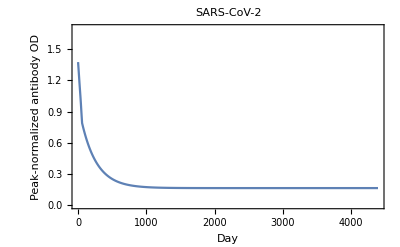

```mathematica
ListLinePlot[sarscov2antibodytimecourseB,
PlotRange->{0, 1.7},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_nOD-by-Day_Pfizer_Booster", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2antibodytimecourseB,
PlotRange->{0, 1.7},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Peak-normalized antibody OD"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_nOD-by-Day_Pfizer_Booster04May2023.pdf.

$Failed

### SARS-CoV-2 Probability of Infection | Antibody OD

```mathematica
sarscov2probinfgivenaod[aod_]:=1/(1+Exp[-(-5.841733+-5.323444*aod)])
```

These values for a and b come from the ancestral and descendent states natural infection analysis to determine them for the zoonotic coronaviruses given baselines and declines for all viruses, and a’s and b’s for the “seasonal” coronaviruses. See Townsend et al. 2021 “The durability of immunity against reinfection by SARS-CoV-2: a comparative evolutionary study”, The Lancet Microbe.

```mathematica
sarscov2probinfgivenaod[aod]
```

1/(1+ⅇ^(5.84173+5.32344 aod))

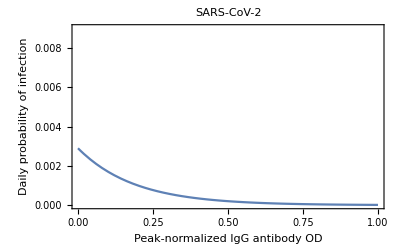

```mathematica
Plot[sarscov2probinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.009},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-nOD_Pfizer_Booster", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Plot[sarscov2probinfgivenaod[x],{x,0,1},
 PlotRange->{0,0.009},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Peak-normalized IgG antibody OD", "Daily probability of infection"}
]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-nOD_Pfizer_Booster04May2023.pdf.

$Failed

```mathematica
sarscov2probinfgivenall[a_, b_, aod_]:=1/(1+Exp[-(a+b*aod)])
```

### SARS-CoV-2 Probability of No Reinfection Time Course

```mathematica
sarscov2probnoreinfectiontimecourse={1};
day=1;
AppendTo[sarscov2probnoreinfectiontimecourse, 
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day+1]]])
];

While[day<4393,
Increment[day];
AppendTo[sarscov2probnoreinfectiontimecourse, 
If[day<Length[sarscov2antibodytimecourseB],
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day+1]] ]),
sarscov2probnoreinfectiontimecourse[[day]]*(1-sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[1201]]])
]
]
];

sarscov2probnoreinfectiontimecourse
```

{1,0.999998,0.999996,0.999994,0.999991,0.999989,0.999986,0.999983,0.999981,0.999978,0.999974,0.999971,0.999967,0.999964,0.99996,0.999956,0.999951,0.999947,0.999942,0.999937,0.999931,0.999925,0.999919,0.999913,0.999907,0.9999,0.999892,0.999885,0.999876,0.999868,0.999859,0.99985,0.99984,0.999829,0.999819,0.999807,0.999795,0.999782,0.999769,0.999755,0.99974,0.999724,0.999707,0.99969,0.999671,0.999651,0.99963,0.999607,0.999584,0.999558,0.999532,0.999503,0.999474,0.999442,0.999409,0.999374,0.999337,0.999298,0.999256,0.999213,0.999169,0.999124,0.999078,0.999032,0.998985,0.998938,0.998889,0.998841,0.998791,0.998741,0.99869,0.998638,0.998585,0.998532,0.998478,0.998424,0.998368,0.998312,0.998255,0.998197,0.998139,0.998079,0.998019,0.997958,0.997897,0.997834,0.997771,0.997706,0.997641,0.997575,0.997509,0.997441,0.997373,0.997303,0.997233,0.997162,0.99709,0.997017,0.996943,0.996868,0.996792,0.996716,0.996638,0.99656,0.99648,0.9964,0.996318,0.996236,0.996153,0.996068,0.995983,0.995897,0.995809,0.995721,0.995631,0.995541,0.99545,0.995357,0.995263,0.995169,0.995073,0.994976,0.994878,0.994779,0.994679,0.994578,0.994476,0.994373,0.994268,0.994162,0.994056,0.993948,0.993839,0.993728,0.993617,0.993504,0.993391,0.993276,0.99316,0.993042,0.992924,0.992804,0.992683,0.992561,0.992437,0.992313,0.992187,0.992059,0.991931,0.991801,0.99167,0.991538,0.991404,0.99127,0.991133,0.990996,0.990857,0.990717,0.990576,0.990433,0.990289,0.990143,0.989997,0.989848,0.989699,0.989548,0.989396,0.989242,0.989087,0.988931,0.988773,0.988614,0.988453,0.988291,0.988128,0.987963,0.987796,0.987629,0.98746,0.987289,0.987117,0.986943,0.986768,0.986592,0.986414,0.986234,0.986053,0.985871,0.985687,0.985502,0.985315,0.985126,0.984936,0.984745,0.984552,0.984357,0.984161,0.983963,0.983764,0.983564,0.983361,0.983157,0.982952,0.982745,0.982536,0.982326,0.982115,0.981901,0.981686,0.98147,0.981252,0.981032,0.980811,0.980588,0.980363,0.980137,0.97991,0.97968,0.979449,0.979217,0.978982,0.978746,0.978509,0.97827,0.978029,0.977786,0.977542,0.977296,0.977049,0.976799,0.976549,0.976296,0.976042,0.975786,0.975529,0.975269,0.975008,0.974746,0.974482,0.974216,0.973948,0.973679,0.973407,0.973135,0.97286,0.972584,0.972306,0.972027,0.971745,0.971462,0.971177,0.970891,0.970603,0.970313,0.970021,0.969728,0.969433,0.969136,0.968837,0.968537,0.968235,0.967931,0.967626,0.967319,0.96701,0.966699,0.966387,0.966072,0.965756,0.965439,0.965119,0.964798,0.964475,0.964151,0.963824,0.963496,0.963166,0.962835,0.962501,0.962166,0.961829,0.961491,0.96115,0.960808,0.960465,0.960119,0.959772,0.959423,0.959072,0.958719,0.958365,0.958009,0.957651,0.957291,0.95693,0.956567,0.956202,0.955836,0.955468,0.955098,0.954726,0.954353,0.953977,0.9536,0.953222,0.952841,0.952459,0.952075,0.95169,0.951302,0.950913,0.950523,0.95013,0.949736,0.94934,0.948942,0.948543,0.948142,0.947739,0.947335,0.946929,0.946521,0.946111,0.9457,0.945287,0.944872,0.944456,0.944038,0.943618,0.943196,0.942773,0.942348,0.941922,0.941494,0.941064,0.940632,0.940199,0.939764,0.939328,0.93889,0.93845,0.938008,0.937565,0.93712,0.936674,0.936226,0.935776,0.935325,0.934872,0.934417,0.933961,0.933503,0.933043,0.932582,0.932119,0.931655,0.931189,0.930722,0.930252,0.929782,0.929309,0.928835,0.92836,0.927883,0.927404,0.926924,0.926442,0.925959,0.925474,0.924987,0.924499,0.92401,0.923518,0.923026,0.922532,0.922036,0.921539,0.92104,0.920539,0.920038,0.919534,0.919029,0.918523,0.918015,0.917506,0.916995,0.916483,0.915969,0.915454,0.914937,0.914419,0.913899,0.913378,0.912855,0.912331,0.911806,0.911279,0.910751,0.910221,0.90969,0.909157,0.908623,0.908088,0.907551,0.907013,0.906473,0.905932,0.90539,0.904846,0.904301,0.903755,0.903207,0.902658,0.902107,0.901555,0.901002,0.900448,0.899892,0.899334,0.898776,0.898216,0.897655,0.897092,0.896529,0.895964,0.895397,0.89483,0.894261,0.893691,0.893119,0.892547,0.891973,0.891397,0.890821,0.890243,0.889665,0.889084,0.888503,0.887921,0.887337,0.886752,0.886166,0.885578,0.88499,0.8844,0.883809,0.883217,0.882624,0.882029,0.881434,0.880837,0.880239,0.87964,0.87904,0.878439,0.877837,0.877233,0.876629,0.876023,0.875417,0.874809,0.8742,0.87359,0.872979,0.872367,0.871754,0.871139,0.870524,0.869908,0.86929,0.868672,0.868053,0.867432,0.866811,0.866188,0.865565,0.86494,0.864315,0.863689,0.863061,0.862433,0.861804,0.861173,0.860542,0.85991,0.859277,0.858643,0.858008,0.857372,0.856735,0.856097,0.855459,0.854819,0.854179,0.853537,0.852895,0.852252,0.851608,0.850963,0.850318,0.849671,0.849024,0.848375,0.847726,0.847077,0.846426,0.845774,0.845122,0.844469,0.843815,0.84316,0.842505,0.841848,0.841191,0.840533,0.839875,0.839216,0.838555,0.837895,0.837233,0.836571,0.835907,0.835244,0.834579,0.833914,0.833248,0.832581,0.831914,0.831246,0.830577,0.829908,0.829238,0.828567,0.827896,0.827224,0.826551,0.825878,0.825204,0.824529,0.823854,0.823178,0.822502,0.821824,0.821147,0.820469,0.81979,0.81911,0.81843,0.81775,0.817068,0.816387,0.815704,0.815021,0.814338,0.813654,0.81297,0.812284,0.811599,0.810913,0.810226,0.809539,0.808852,0.808163,0.807475,0.806786,0.806096,0.805406,0.804716,0.804025,0.803333,0.802641,0.801949,0.801256,0.800563,0.799869,0.799175,0.79848,0.797785,0.79709,0.796394,0.795698,0.795001,0.794304,0.793607,0.792909,0.792211,0.791513,0.790814,0.790114,0.789415,0.788715,0.788014,0.787314,0.786613,0.785911,0.78521,0.784508,0.783806,0.783103,0.7824,0.781697,0.780993,0.780289,0.779585,0.778881,0.778176,0.777471,0.776766,0.776061,0.775355,0.774649,0.773942,0.773236,0.772529,0.771822,0.771115,0.770408,0.7697,0.768992,0.768284,0.767576,0.766867,0.766158,0.765449,0.76474,0.764031,0.763322,0.762612,0.761902,0.761192,0.760482,0.759772,0.759061,0.758351,0.75764,0.756929,0.756218,0.755507,0.754795,0.754084,0.753372,0.752661,0.751949,0.751237,0.750525,0.749813,0.749101,0.748388,0.747676,0.746963,0.746251,0.745538,0.744826,0.744113,0.7434,0.742687,0.741974,0.741261,0.740548,0.739835,0.739122,0.738409,0.737696,0.736982,0.736269,0.735556,0.734843,0.734129,0.733416,0.732703,0.73199,0.731276,0.730563,0.72985,0.729136,0.728423,0.72771,0.726997,0.726284,0.72557,0.724857,0.724144,0.723431,0.722718,0.722005,0.721293,0.72058,0.719867,0.719154,0.718442,0.717729,0.717017,0.716304,0.715592,0.71488,0.714168,0.713456,0.712744,0.712032,0.71132,0.710609,0.709897,0.709186,0.708474,0.707763,0.707052,0.706341,0.70563,0.70492,0.704209,0.703499,0.702788,0.702078,0.701368,0.700659,0.699949,0.699239,0.69853,0.697821,0.697112,0.696403,0.695694,0.694986,0.694278,0.693569,0.692861,0.692154,0.691446,0.690739,0.690031,0.689324,0.688618,0.687911,0.687205,0.686498,0.685792,0.685087,0.684381,0.683676,0.682971,0.682266,0.681561,0.680857,0.680153,0.679449,0.678745,0.678041,0.677338,0.676635,0.675932,0.67523,0.674528,0.673826,0.673124,0.672423,0.671721,0.67102,0.67032,0.669619,0.668919,0.668219,0.66752,0.666821,0.666122,0.665423,0.664724,0.664026,0.663328,0.662631,0.661934,0.661237,0.66054,0.659844,0.659148,0.658452,0.657757,0.657061,0.656367,0.655672,0.654978,0.654284,0.653591,0.652898,0.652205,0.651512,0.65082,0.650128,0.649437,0.648745,0.648055,0.647364,0.646674,0.645984,0.645295,0.644605,0.643917,0.643228,0.64254,0.641853,0.641165,0.640478,0.639792,0.639105,0.638419,0.637734,0.637049,0.636364,0.63568,0.634996,0.634312,0.633629,0.632946,0.632263,0.631581,0.6309,0.630218,0.629537,0.628857,0.628177,0.627497,0.626817,0.626138,0.62546,0.624782,0.624104,0.623427,0.62275,0.622073,0.621397,0.620721,0.620046,0.619371,0.618696,0.618022,0.617349,0.616676,0.616003,0.61533,0.614658,0.613987,0.613316,0.612645,0.611975,0.611305,0.610636,0.609967,0.609298,0.60863,0.607962,0.607295,0.606629,0.605962,0.605296,0.604631,0.603966,0.603301,0.602637,0.601974,0.601311,0.600648,0.599986,0.599324,0.598662,0.598001,0.597341,0.596681,0.596022,0.595362,0.594704,0.594046,0.593388,0.592731,0.592074,0.591418,0.590762,0.590107,0.589452,0.588798,0.588144,0.58749,0.586837,0.586185,0.585533,0.584881,0.58423,0.58358,0.58293,0.58228,0.581631,0.580982,0.580334,0.579687,0.57904,0.578393,0.577747,0.577101,0.576456,0.575811,0.575167,0.574523,0.57388,0.573237,0.572595,0.571954,0.571312,0.570672,0.570031,0.569392,0.568752,0.568114,0.567476,0.566838,0.566201,0.565564,0.564928,0.564292,0.563657,0.563022,0.562388,0.561755,0.561121,0.560489,0.559857,0.559225,0.558594,0.557964,0.557334,0.556704,0.556075,0.555447,0.554819,0.554191,0.553564,0.552938,0.552312,0.551687,0.551062,0.550438,0.549814,0.54919,0.548568,0.547945,0.547324,0.546703,0.546082,0.545462,0.544842,0.544223,0.543605,0.542987,0.542369,0.541752,0.541136,0.54052,0.539905,0.53929,0.538676,0.538062,0.537449,0.536836,0.536224,0.535612,0.535001,0.534391,0.533781,0.533171,0.532562,0.531954,0.531346,0.530739,0.530132,0.529526,0.52892,0.528315,0.52771,0.527106,0.526503,0.5259,0.525297,0.524696,0.524094,0.523493,0.522893,0.522293,0.521694,0.521096,0.520497,0.5199,0.519303,0.518706,0.518111,0.517515,0.51692,0.516326,0.515732,0.515139,0.514547,0.513955,0.513363,0.512772,0.512182,0.511592,0.511002,0.510414,0.509825,0.509238,0.508651,0.508064,0.507478,0.506892,0.506307,0.505723,0.505139,0.504556,0.503973,0.503391,0.502809,0.502228,0.501648,0.501068,0.500488,0.499909,0.499331,0.498753,0.498176,0.4976,0.497023,0.496448,0.495873,0.495298,0.494725,0.494151,0.493578,0.493006,0.492434,0.491863,0.491293,0.490723,0.490153,0.489584,0.489016,0.488448,0.487881,0.487314,0.486748,0.486182,0.485617,0.485053,0.484489,0.483926,0.483363,0.482801,0.482239,0.481678,0.481117,0.480557,0.479998,0.479439,0.47888,0.478322,0.477765,0.477208,0.476652,0.476097,0.475542,0.474987,0.474433,0.47388,0.473327,0.472775,0.472223,0.471672,0.471121,0.470571,0.470022,0.469473,0.468924,0.468376,0.467829,0.467282,0.466736,0.46619,0.465645,0.465101,0.464557,0.464013,0.463471,0.462928,0.462386,0.461845,0.461305,0.460764,0.460225,0.459686,0.459147,0.45861,0.458072,0.457535,0.456999,0.456463,0.455928,0.455394,0.45486,0.454326,0.453793,0.453261,0.452729,0.452198,0.451667,0.451137,0.450607,0.450078,0.44955,0.449022,0.448494,0.447967,0.447441,0.446915,0.44639,0.445865,0.445341,0.444817,0.444294,0.443772,0.44325,0.442728,0.442208,0.441687,0.441168,0.440648,0.44013,0.439611,0.439094,0.438577,0.43806,0.437544,0.437029,0.436514,0.436,0.435486,0.434973,0.43446,0.433948,0.433436,0.432925,0.432415,0.431905,0.431395,0.430887,0.430378,0.42987,0.429363,0.428856,0.42835,0.427845,0.42734,0.426835,0.426331,0.425827,0.425325,0.424822,0.42432,0.423819,0.423318,0.422818,0.422318,0.421819,0.42132,0.420822,0.420325,0.419828,0.419331,0.418835,0.41834,0.417845,0.417351,0.416857,0.416364,0.415871,0.415379,0.414887,0.414396,0.413905,0.413415,0.412926,0.412437,0.411948,0.41146,0.410973,0.410486,0.409999,0.409514,0.409028,0.408543,0.408059,0.407576,0.407092,0.40661,0.406128,0.405646,0.405165,0.404684,0.404204,0.403725,0.403246,0.402767,0.402289,0.401812,0.401335,0.400859,0.400383,0.399908,0.399433,0.398959,0.398485,0.398012,0.397539,0.397067,0.396595,0.396124,0.395653,0.395183,0.394714,0.394245,0.393776,0.393308,0.392841,0.392374,0.391907,0.391441,0.390976,0.390511,0.390047,0.389583,0.389119,0.388657,0.388194,0.387732,0.387271,0.38681,0.38635,0.38589,0.385431,0.384972,0.384514,0.384056,0.383599,0.383142,0.382686,0.382231,0.381775,0.381321,0.380867,0.380413,0.37996,0.379507,0.379055,0.378603,0.378152,0.377702,0.377252,0.376802,0.376353,0.375904,0.375456,0.375009,0.374562,0.374115,0.373669,0.373223,0.372778,0.372334,0.37189,0.371446,0.371003,0.37056,0.370118,0.369677,0.369236,0.368795,0.368355,0.367916,0.367476,0.367038,0.3666,0.366162,0.365725,0.365289,0.364852,0.364417,0.363982,0.363547,0.363113,0.362679,0.362246,0.361813,0.361381,0.36095,0.360518,0.360088,0.359658,0.359228,0.358799,0.35837,0.357942,0.357514,0.357086,0.35666,0.356233,0.355808,0.355382,0.354957,0.354533,0.354109,0.353686,0.353263,0.35284,0.352418,0.351997,0.351576,0.351155,0.350735,0.350316,0.349897,0.349478,0.34906,0.348642,0.348225,0.347809,0.347392,0.346977,0.346561,0.346147,0.345732,0.345319,0.344905,0.344492,0.34408,0.343668,0.343257,0.342846,0.342435,0.342025,0.341615,0.341206,0.340798,0.34039,0.339982,0.339575,0.339168,0.338762,0.338356,0.33795,0.337546,0.337141,0.336737,0.336334,0.335931,0.335528,0.335126,0.334724,0.334323,0.333923,0.333522,0.333123,0.332723,0.332324,0.331926,0.331528,0.331131,0.330734,0.330337,0.329941,0.329545,0.32915,0.328755,0.328361,0.327967,0.327574,0.327181,0.326789,0.326397,0.326005,0.325614,0.325224,0.324833,0.324444,0.324054,0.323666,0.323277,0.322889,0.322502,0.322115,0.321728,0.321342,0.320956,0.320571,0.320186,0.319802,0.319418,0.319035,0.318652,0.318269,0.317887,0.317506,0.317124,0.316744,0.316363,0.315983,0.315604,0.315225,0.314847,0.314468,0.314091,0.313714,0.313337,0.31296,0.312584,0.312209,0.311834,0.311459,0.311085,0.310712,0.310338,0.309965,0.309593,0.309221,0.308849,0.308478,0.308108,0.307737,0.307368,0.306998,0.306629,0.306261,0.305893,0.305525,0.305158,0.304791,0.304425,0.304059,0.303693,0.303328,0.302964,0.302599,0.302236,0.301872,0.301509,0.301147,0.300785,0.300423,0.300062,0.299701,0.299341,0.298981,0.298621,0.298262,0.297903,0.297545,0.297187,0.29683,0.296473,0.296116,0.29576,0.295404,0.295049,0.294694,0.294339,0.293985,0.293631,0.293278,0.292925,0.292573,0.292221,0.291869,0.291518,0.291167,0.290817,0.290467,0.290117,0.289768,0.289419,0.289071,0.288723,0.288376,0.288029,0.287682,0.287336,0.28699,0.286644,0.286299,0.285955,0.285611,0.285267,0.284923,0.28458,0.284238,0.283895,0.283554,0.283212,0.282871,0.282531,0.28219,0.281851,0.281511,0.281172,0.280834,0.280496,0.280158,0.27982,0.279483,0.279147,0.278811,0.278475,0.278139,0.277804,0.27747,0.277136,0.276802,0.276468,0.276135,0.275803,0.27547,0.275139,0.274807,0.274476,0.274145,0.273815,0.273485,0.273156,0.272827,0.272498,0.27217,0.271842,0.271514,0.271187,0.27086,0.270534,0.270208,0.269882,0.269557,0.269232,0.268908,0.268583,0.26826,0.267936,0.267614,0.267291,0.266969,0.266647,0.266326,0.266005,0.265684,0.265364,0.265044,0.264724,0.264405,0.264087,0.263768,0.26345,0.263133,0.262815,0.262499,0.262182,0.261866,0.26155,0.261235,0.26092,0.260605,0.260291,0.259977,0.259664,0.259351,0.259038,0.258726,0.258414,0.258102,0.257791,0.25748,0.257169,0.256859,0.256549,0.25624,0.255931,0.255622,0.255314,0.255006,0.254699,0.254391,0.254084,0.253778,0.253472,0.253166,0.252861,0.252556,0.252251,0.251947,0.251643,0.251339,0.251036,0.250733,0.250431,0.250129,0.249827,0.249526,0.249225,0.248924,0.248623,0.248324,0.248024,0.247725,0.247426,0.247127,0.246829,0.246531,0.246234,0.245937,0.24564,0.245343,0.245047,0.244752,0.244456,0.244161,0.243867,0.243572,0.243278,0.242985,0.242692,0.242399,0.242106,0.241814,0.241522,0.241231,0.24094,0.240649,0.240358,0.240068,0.239778,0.239489,0.2392,0.238911,0.238623,0.238335,0.238047,0.23776,0.237473,0.237186,0.2369,0.236614,0.236328,0.236043,0.235758,0.235473,0.235189,0.234905,0.234621,0.234338,0.234055,0.233773,0.23349,0.233209,0.232927,0.232646,0.232365,0.232084,0.231804,0.231524,0.231245,0.230965,0.230687,0.230408,0.23013,0.229852,0.229574,0.229297,0.22902,0.228744,0.228468,0.228192,0.227916,0.227641,0.227366,0.227091,0.226817,0.226543,0.22627,0.225996,0.225723,0.225451,0.225179,0.224907,0.224635,0.224364,0.224093,0.223822,0.223552,0.223282,0.223012,0.222743,0.222474,0.222205,0.221936,0.221668,0.221401,0.221133,0.220866,0.220599,0.220333,0.220067,0.219801,0.219535,0.21927,0.219005,0.218741,0.218476,0.218213,0.217949,0.217686,0.217423,0.21716,0.216898,0.216636,0.216374,0.216112,0.215851,0.215591,0.21533,0.21507,0.21481,0.214551,0.214291,0.214032,0.213774,0.213516,0.213258,0.213,0.212743,0.212486,0.212229,0.211972,0.211716,0.21146,0.211205,0.21095,0.210695,0.21044,0.210186,0.209932,0.209678,0.209425,0.209172,0.208919,0.208667,0.208414,0.208163,0.207911,0.20766,0.207409,0.207158,0.206908,0.206658,0.206408,0.206159,0.205909,0.205661,0.205412,0.205164,0.204916,0.204668,0.204421,0.204174,0.203927,0.203681,0.203434,0.203189,0.202943,0.202698,0.202453,0.202208,0.201964,0.20172,0.201476,0.201232,0.200989,0.200746,0.200503,0.200261,0.200019,0.199777,0.199536,0.199295,0.199054,0.198813,0.198573,0.198333,0.198093,0.197854,0.197614,0.197375,0.197137,0.196899,0.196661,0.196423,0.196185,0.195948,0.195711,0.195475,0.195238,0.195002,0.194767,0.194531,0.194296,0.194061,0.193827,0.193592,0.193358,0.193124,0.192891,0.192658,0.192425,0.192192,0.19196,0.191728,0.191496,0.191265,0.191033,0.190802,0.190572,0.190341,0.190111,0.189881,0.189652,0.189422,0.189193,0.188965,0.188736,0.188508,0.18828,0.188052,0.187825,0.187598,0.187371,0.187145,0.186918,0.186692,0.186467,0.186241,0.186016,0.185791,0.185566,0.185342,0.185118,0.184894,0.18467,0.184447,0.184224,0.184001,0.183779,0.183557,0.183335,0.183113,0.182891,0.18267,0.182449,0.182229,0.182008,0.181788,0.181569,0.181349,0.18113,0.180911,0.180692,0.180473,0.180255,0.180037,0.179819,0.179602,0.179385,0.179168,0.178951,0.178735,0.178519,0.178303,0.178087,0.177872,0.177657,0.177442,0.177227,0.177013,0.176799,0.176585,0.176371,0.176158,0.175945,0.175732,0.17552,0.175307,0.175095,0.174884,0.174672,0.174461,0.17425,0.174039,0.173829,0.173618,0.173408,0.173199,0.172989,0.17278,0.172571,0.172362,0.172154,0.171946,0.171738,0.17153,0.171322,0.171115,0.170908,0.170702,0.170495,0.170289,0.170083,0.169877,0.169672,0.169466,0.169261,0.169057,0.168852,0.168648,0.168444,0.16824,0.168037,0.167834,0.167631,0.167428,0.167225,0.167023,0.166821,0.166619,0.166418,0.166216,0.166015,0.165814,0.165614,0.165414,0.165213,0.165014,0.164814,0.164615,0.164416,0.164217,0.164018,0.16382,0.163621,0.163423,0.163226,0.163028,0.162831,0.162634,0.162437,0.162241,0.162045,0.161849,0.161653,0.161457,0.161262,0.161067,0.160872,0.160677,0.160483,0.160289,0.160095,0.159901,0.159708,0.159515,0.159322,0.159129,0.158936,0.158744,0.158552,0.15836,0.158169,0.157977,0.157786,0.157595,0.157405,0.157214,0.157024,0.156834,0.156644,0.156455,0.156266,0.156077,0.155888,0.155699,0.155511,0.155323,0.155135,0.154947,0.15476,0.154572,0.154385,0.154199,0.154012,0.153826,0.15364,0.153454,0.153268,0.153083,0.152897,0.152712,0.152528,0.152343,0.152159,0.151975,0.151791,0.151607,0.151424,0.151241,0.151058,0.150875,0.150692,0.15051,0.150328,0.150146,0.149964,0.149783,0.149602,0.149421,0.14924,0.149059,0.148879,0.148699,0.148519,0.148339,0.14816,0.147981,0.147801,0.147623,0.147444,0.147266,0.147087,0.146909,0.146732,0.146554,0.146377,0.1462,0.146023,0.145846,0.14567,0.145493,0.145317,0.145142,0.144966,0.144791,0.144615,0.14444,0.144266,0.144091,0.143917,0.143743,0.143569,0.143395,0.143221,0.143048,0.142875,0.142702,0.142529,0.142357,0.142185,0.142013,0.141841,0.141669,0.141498,0.141327,0.141156,0.140985,0.140814,0.140644,0.140474,0.140304,0.140134,0.139964,0.139795,0.139626,0.139457,0.139288,0.13912,0.138951,0.138783,0.138615,0.138447,0.13828,0.138113,0.137945,0.137778,0.137612,0.137445,0.137279,0.137113,0.136947,0.136781,0.136616,0.13645,0.136285,0.13612,0.135956,0.135791,0.135627,0.135463,0.135299,0.135135,0.134971,0.134808,0.134645,0.134482,0.134319,0.134157,0.133994,0.133832,0.13367,0.133509,0.133347,0.133186,0.133024,0.132864,0.132703,0.132542,0.132382,0.132222,0.132062,0.131902,0.131742,0.131583,0.131423,0.131264,0.131106,0.130947,0.130788,0.13063,0.130472,0.130314,0.130156,0.129999,0.129842,0.129685,0.129528,0.129371,0.129214,0.129058,0.128902,0.128746,0.12859,0.128434,0.128279,0.128124,0.127969,0.127814,0.127659,0.127505,0.12735,0.127196,0.127042,0.126888,0.126735,0.126582,0.126428,0.126275,0.126123,0.12597,0.125817,0.125665,0.125513,0.125361,0.125209,0.125058,0.124907,0.124755,0.124604,0.124454,0.124303,0.124153,0.124002,0.123852,0.123702,0.123553,0.123403,0.123254,0.123105,0.122956,0.122807,0.122658,0.12251,0.122362,0.122213,0.122066,0.121918,0.12177,0.121623,0.121476,0.121329,0.121182,0.121035,0.120889,0.120742,0.120596,0.12045,0.120305,0.120159,0.120014,0.119868,0.119723,0.119578,0.119434,0.119289,0.119145,0.119,0.118856,0.118713,0.118569,0.118425,0.118282,0.118139,0.117996,0.117853,0.117711,0.117568,0.117426,0.117284,0.117142,0.117,0.116858,0.116717,0.116576,0.116435,0.116294,0.116153,0.116012,0.115872,0.115732,0.115592,0.115452,0.115312,0.115172,0.115033,0.114894,0.114755,0.114616,0.114477,0.114339,0.1142,0.114062,0.113924,0.113786,0.113648,0.113511,0.113373,0.113236,0.113099,0.112962,0.112826,0.112689,0.112553,0.112416,0.11228,0.112144,0.112009,0.111873,0.111738,0.111603,0.111467,0.111333,0.111198,0.111063,0.110929,0.110795,0.11066,0.110526,0.110393,0.110259,0.110126,0.109992,0.109859,0.109726,0.109593,0.109461,0.109328,0.109196,0.109064,0.108932,0.1088,0.108668,0.108537,0.108405,0.108274,0.108143,0.108012,0.107882,0.107751,0.107621,0.10749,0.10736,0.10723,0.1071,0.106971,0.106841,0.106712,0.106583,0.106454,0.106325,0.106196,0.106068,0.105939,0.105811,0.105683,0.105555,0.105427,0.1053,0.105172,0.105045,0.104918,0.104791,0.104664,0.104537,0.104411,0.104285,0.104158,0.104032,0.103906,0.103781,0.103655,0.10353,0.103404,0.103279,0.103154,0.103029,0.102904,0.10278,0.102656,0.102531,0.102407,0.102283,0.102159,0.102036,0.101912,0.101789,0.101666,0.101543,0.10142,0.101297,0.101174,0.101052,0.10093,0.100807,0.100685,0.100564,0.100442,0.10032,0.100199,0.100078,0.0999565,0.0998355,0.0997146,0.0995939,0.0994734,0.099353,0.0992327,0.0991126,0.0989927,0.0988728,0.0987532,0.0986336,0.0985142,0.098395,0.0982759,0.098157,0.0980381,0.0979195,0.097801,0.0976826,0.0975643,0.0974463,0.0973283,0.0972105,0.0970928,0.0969753,0.0968579,0.0967407,0.0966236,0.0965066,0.0963898,0.0962732,0.0961566,0.0960402,0.095924,0.0958079,0.0956919,0.0955761,0.0954604,0.0953449,0.0952295,0.0951142,0.0949991,0.0948841,0.0947692,0.0946545,0.09454,0.0944255,0.0943112,0.0941971,0.0940831,0.0939692,0.0938554,0.0937418,0.0936284,0.093515,0.0934018,0.0932888,0.0931759,0.0930631,0.0929504,0.0928379,0.0927256,0.0926133,0.0925012,0.0923893,0.0922774,0.0921657,0.0920542,0.0919427,0.0918315,0.0917203,0.0916093,0.0914984,0.0913876,0.091277,0.0911665,0.0910562,0.090946,0.0908359,0.0907259,0.0906161,0.0905064,0.0903969,0.0902875,0.0901782,0.090069,0.08996,0.0898511,0.0897424,0.0896337,0.0895252,0.0894169,0.0893086,0.0892005,0.0890926,0.0889847,0.088877,0.0887694,0.088662,0.0885547,0.0884475,0.0883404,0.0882335,0.0881267,0.08802,0.0879135,0.087807,0.0877008,0.0875946,0.0874886,0.0873827,0.0872769,0.0871713,0.0870657,0.0869604,0.0868551,0.08675,0.086645,0.0865401,0.0864353,0.0863307,0.0862262,0.0861218,0.0860176,0.0859135,0.0858095,0.0857056,0.0856019,0.0854982,0.0853948,0.0852914,0.0851882,0.085085,0.084982,0.0848792,0.0847764,0.0846738,0.0845713,0.084469,0.0843667,0.0842646,0.0841626,0.0840607,0.083959,0.0838573,0.0837558,0.0836544,0.0835532,0.083452,0.083351,0.0832501,0.0831494,0.0830487,0.0829482,0.0828478,0.0827475,0.0826473,0.0825473,0.0824474,0.0823476,0.0822479,0.0821483,0.0820489,0.0819496,0.0818504,0.0817513,0.0816524,0.0815535,0.0814548,0.0813562,0.0812577,0.0811594,0.0810611,0.080963,0.080865,0.0807671,0.0806694,0.0805717,0.0804742,0.0803768,0.0802795,0.0801823,0.0800852,0.0799883,0.0798915,0.0797948,0.0796982,0.0796017,0.0795054,0.0794091,0.079313,0.079217,0.0791211,0.0790253,0.0789297,0.0788341,0.0787387,0.0786434,0.0785482,0.0784531,0.0783582,0.0782633,0.0781686,0.0780739,0.0779794,0.0778851,0.0777908,0.0776966,0.0776026,0.0775086,0.0774148,0.0773211,0.0772275,0.077134,0.0770406,0.0769474,0.0768543,0.0767612,0.0766683,0.0765755,0.0764828,0.0763902,0.0762978,0.0762054,0.0761132,0.076021,0.075929,0.0758371,0.0757453,0.0756536,0.075562,0.0754706,0.0753792,0.075288,0.0751968,0.0751058,0.0750149,0.0749241,0.0748334,0.0747428,0.0746523,0.074562,0.0744717,0.0743816,0.0742915,0.0742016,0.0741118,0.0740221,0.0739325,0.073843,0.0737536,0.0736643,0.0735751,0.0734861,0.0733971,0.0733083,0.0732195,0.0731309,0.0730424,0.072954,0.0728657,0.0727775,0.0726894,0.0726014,0.0725135,0.0724257,0.072338,0.0722505,0.072163,0.0720757,0.0719884,0.0719013,0.0718142,0.0717273,0.0716405,0.0715538,0.0714672,0.0713806,0.0712942,0.0712079,0.0711217,0.0710357,0.0709497,0.0708638,0.070778,0.0706923,0.0706068,0.0705213,0.0704359,0.0703507,0.0702655,0.0701804,0.0700955,0.0700106,0.0699259,0.0698412,0.0697567,0.0696723,0.0695879,0.0695037,0.0694196,0.0693355,0.0692516,0.0691678,0.069084,0.0690004,0.0689169,0.0688335,0.0687501,0.0686669,0.0685838,0.0685008,0.0684179,0.068335,0.0682523,0.0681697,0.0680872,0.0680048,0.0679225,0.0678402,0.0677581,0.0676761,0.0675942,0.0675123,0.0674306,0.067349,0.0672675,0.067186,0.0671047,0.0670235,0.0669424,0.0668613,0.0667804,0.0666996,0.0666188,0.0665382,0.0664576,0.0663772,0.0662968,0.0662166,0.0661364,0.0660564,0.0659764,0.0658965,0.0658168,0.0657371,0.0656575,0.065578,0.0654987,0.0654194,0.0653402,0.0652611,0.0651821,0.0651032,0.0650244,0.0649457,0.0648671,0.0647885,0.0647101,0.0646318,0.0645535,0.0644754,0.0643974,0.0643194,0.0642415,0.0641638,0.0640861,0.0640085,0.0639311,0.0638537,0.0637764,0.0636992,0.0636221,0.063545,0.0634681,0.0633913,0.0633146,0.0632379,0.0631614,0.0630849,0.0630085,0.0629323,0.0628561,0.06278,0.062704,0.0626281,0.0625523,0.0624766,0.0624009,0.0623254,0.06225,0.0621746,0.0620994,0.0620242,0.0619491,0.0618741,0.0617992,0.0617244,0.0616497,0.0615751,0.0615005,0.0614261,0.0613517,0.0612775,0.0612033,0.0611292,0.0610552,0.0609813,0.0609075,0.0608337,0.0607601,0.0606865,0.0606131,0.0605397,0.0604664,0.0603932,0.0603201,0.0602471,0.0601742,0.0601013,0.0600286,0.0599559,0.0598833,0.0598109,0.0597385,0.0596661,0.0595939,0.0595218,0.0594497,0.0593778,0.0593059,0.0592341,0.0591624,0.0590908,0.0590192,0.0589478,0.0588764,0.0588052,0.058734,0.0586629,0.0585919,0.058521,0.0584501,0.0583794,0.0583087,0.0582381,0.0581676,0.0580972,0.0580269,0.0579566,0.0578865,0.0578164,0.0577464,0.0576765,0.0576067,0.057537,0.0574673,0.0573977,0.0573283,0.0572589,0.0571896,0.0571203,0.0570512,0.0569821,0.0569131,0.0568443,0.0567754,0.0567067,0.0566381,0.0565695,0.056501,0.0564326,0.0563643,0.0562961,0.0562279,0.0561599,0.0560919,0.056024,0.0559562,0.0558884,0.0558208,0.0557532,0.0556857,0.0556183,0.055551,0.0554838,0.0554166,0.0553495,0.0552825,0.0552156,0.0551487,0.055082,0.0550153,0.0549487,0.0548822,0.0548158,0.0547494,0.0546831,0.0546169,0.0545508,0.0544848,0.0544188,0.054353,0.0542872,0.0542214,0.0541558,0.0540903,0.0540248,0.0539594,0.0538941,0.0538288,0.0537637,0.0536986,0.0536336,0.0535687,0.0535038,0.053439,0.0533744,0.0533097,0.0532452,0.0531808,0.0531164,0.0530521,0.0529879,0.0529237,0.0528597,0.0527957,0.0527318,0.0526679,0.0526042,0.0525405,0.0524769,0.0524134,0.0523499,0.0522866,0.0522233,0.05216,0.0520969,0.0520338,0.0519708,0.0519079,0.0518451,0.0517823,0.0517197,0.0516571,0.0515945,0.0515321,0.0514697,0.0514074,0.0513452,0.051283,0.0512209,0.0511589,0.051097,0.0510351,0.0509734,0.0509116,0.05085,0.0507885,0.050727,0.0506656,0.0506042,0.050543,0.0504818,0.0504207,0.0503597,0.0502987,0.0502378,0.050177,0.0501163,0.0500556,0.049995,0.0499345,0.049874,0.0498137,0.0497534,0.0496931,0.049633,0.0495729,0.0495129,0.049453,0.0493931,0.0493333,0.0492736,0.0492139,0.0491544,0.0490949,0.0490354,0.0489761,0.0489168,0.0488576,0.0487984,0.0487394,0.0486804,0.0486214,0.0485626,0.0485038,0.0484451,0.0483864,0.0483279,0.0482693,0.0482109,0.0481526,0.0480943,0.0480361,0.0479779,0.0479198,0.0478618,0.0478039,0.047746,0.0476882,0.0476305,0.0475728,0.0475152,0.0474577,0.0474003,0.0473429,0.0472856,0.0472283,0.0471712,0.0471141,0.047057,0.0470001,0.0469432,0.0468864,0.0468296,0.0467729,0.0467163,0.0466597,0.0466033,0.0465468,0.0464905,0.0464342,0.046378,0.0463219,0.0462658,0.0462098,0.0461539,0.046098,0.0460422,0.0459864,0.0459308,0.0458752,0.0458196,0.0457642,0.0457088,0.0456535,0.0455982,0.045543,0.0454879,0.0454328,0.0453778,0.0453229,0.045268,0.0452132,0.0451585,0.0451038,0.0450492,0.0449947,0.0449402,0.0448858,0.0448315,0.0447772,0.044723,0.0446689,0.0446148,0.0445608,0.0445068,0.044453,0.0443992,0.0443454,0.0442917,0.0442381,0.0441846,0.0441311,0.0440777,0.0440243,0.043971,0.0439178,0.0438646,0.0438115,0.0437585,0.0437055,0.0436526,0.0435998,0.043547,0.0434943,0.0434416,0.043389,0.0433365,0.043284,0.0432316,0.0431793,0.043127,0.0430748,0.0430227,0.0429706,0.0429186,0.0428666,0.0428148,0.0427629,0.0427112,0.0426595,0.0426078,0.0425562,0.0425047,0.0424533,0.0424019,0.0423506,0.0422993,0.0422481,0.0421969,0.0421459,0.0420948,0.0420439,0.041993,0.0419422,0.0418914,0.0418407,0.04179,0.0417394,0.0416889,0.0416384,0.041588,0.0415377,0.0414874,0.0414372,0.041387,0.0413369,0.0412869,0.0412369,0.041187,0.0411371,0.0410873,0.0410376,0.0409879,0.0409383,0.0408888,0.0408393,0.0407898,0.0407404,0.0406911,0.0406419,0.0405927,0.0405435,0.0404945,0.0404454,0.0403965,0.0403476,0.0402987,0.04025,0.0402012,0.0401526,0.040104,0.0400554,0.0400069,0.0399585,0.0399101,0.0398618,0.0398136,0.0397654,0.0397172,0.0396691,0.0396211,0.0395732,0.0395253,0.0394774,0.0394296,0.0393819,0.0393342,0.0392866,0.0392391,0.0391916,0.0391441,0.0390967,0.0390494,0.0390021,0.0389549,0.0389078,0.0388607,0.0388136,0.0387666,0.0387197,0.0386728,0.038626,0.0385793,0.0385326,0.0384859,0.0384393,0.0383928,0.0383463,0.0382999,0.0382535,0.0382072,0.038161,0.0381148,0.0380686,0.0380226,0.0379765,0.0379306,0.0378847,0.0378388,0.037793,0.0377472,0.0377015,0.0376559,0.0376103,0.0375648,0.0375193,0.0374739,0.0374285,0.0373832,0.037338,0.0372928,0.0372476,0.0372025,0.0371575,0.0371125,0.0370676,0.0370227,0.0369779,0.0369332,0.0368884,0.0368438,0.0367992,0.0367546,0.0367102,0.0366657,0.0366213,0.036577,0.0365327,0.0364885,0.0364443,0.0364002,0.0363561,0.0363121,0.0362682,0.0362243,0.0361804,0.0361366,0.0360929,0.0360492,0.0360056,0.035962,0.0359184,0.035875,0.0358315,0.0357882,0.0357448,0.0357016,0.0356583,0.0356152,0.0355721,0.035529,0.035486,0.035443,0.0354001,0.0353573,0.0353145,0.0352717,0.035229,0.0351864,0.0351438,0.0351013,0.0350588,0.0350163,0.0349739,0.0349316,0.0348893,0.0348471,0.0348049,0.0347628,0.0347207,0.0346787,0.0346367,0.0345947,0.0345529,0.034511,0.0344693,0.0344275,0.0343859,0.0343442,0.0343027,0.0342611,0.0342197,0.0341782,0.0341369,0.0340955,0.0340543,0.034013,0.0339719,0.0339308,0.0338897,0.0338487,0.0338077,0.0337668,0.0337259,0.0336851,0.0336443,0.0336035,0.0335629,0.0335222,0.0334817,0.0334411,0.0334007,0.0333602,0.0333198,0.0332795,0.0332392,0.033199,0.0331588,0.0331186,0.0330786,0.0330385,0.0329985,0.0329586,0.0329187,0.0328788,0.032839,0.0327993,0.0327596,0.0327199,0.0326803,0.0326407,0.0326012,0.0325618,0.0325224,0.032483,0.0324437,0.0324044,0.0323652,0.032326,0.0322869,0.0322478,0.0322087,0.0321697,0.0321308,0.0320919,0.0320531,0.0320143,0.0319755,0.0319368,0.0318981,0.0318595,0.031821,0.0317824,0.031744,0.0317055,0.0316672,0.0316288,0.0315905,0.0315523,0.0315141,0.0314759,0.0314378,0.0313998,0.0313618,0.0313238,0.0312859,0.031248,0.0312102,0.0311724,0.0311347,0.031097,0.0310594,0.0310218,0.0309842,0.0309467,0.0309092,0.0308718,0.0308344,0.0307971,0.0307598,0.0307226,0.0306854,0.0306483,0.0306112,0.0305741,0.0305371,0.0305001,0.0304632,0.0304263,0.0303895,0.0303527,0.030316,0.0302793,0.0302426,0.030206,0.0301694,0.0301329,0.0300964,0.03006,0.0300236,0.0299873,0.029951,0.0299147,0.0298785,0.0298423,0.0298062,0.0297701,0.0297341,0.0296981,0.0296622,0.0296263,0.0295904,0.0295546,0.0295188,0.0294831,0.0294474,0.0294117,0.0293761,0.0293406,0.029305,0.0292696,0.0292341,0.0291987,0.0291634,0.0291281,0.0290928,0.0290576,0.0290224,0.0289873,0.0289522,0.0289172,0.0288822,0.0288472,0.0288123,0.0287774,0.0287426,0.0287078,0.028673,0.0286383,0.0286037,0.028569,0.0285344,0.0284999,0.0284654,0.0284309,0.0283965,0.0283622,0.0283278,0.0282935,0.0282593,0.0282251,0.0281909,0.0281568,0.0281227,0.0280886,0.0280546,0.0280207,0.0279868,0.0279529,0.027919,0.0278853,0.0278515,0.0278178,0.0277841,0.0277505,0.0277169,0.0276833,0.0276498,0.0276163,0.0275829,0.0275495,0.0275162,0.0274829,0.0274496,0.0274164,0.0273832,0.02735,0.0273169,0.0272839,0.0272508,0.0272178,0.0271849,0.027152,0.0271191,0.0270863,0.0270535,0.0270208,0.026988,0.0269554,0.0269227,0.0268902,0.0268576,0.0268251,0.0267926,0.0267602,0.0267278,0.0266954,0.0266631,0.0266308,0.0265986,0.0265664,0.0265342,0.0265021,0.02647,0.026438,0.026406,0.026374,0.0263421,0.0263102,0.0262784,0.0262466,0.0262148,0.0261831,0.0261514,0.0261197,0.0260881,0.0260565,0.026025,0.0259935,0.025962,0.0259306,0.0258992,0.0258678,0.0258365,0.0258052,0.025774,0.0257428,0.0257116,0.0256805,0.0256494,0.0256184,0.0255874,0.0255564,0.0255255,0.0254946,0.0254637,0.0254329,0.0254021,0.0253713,0.0253406,0.0253099,0.0252793,0.0252487,0.0252181,0.0251876,0.0251571,0.0251267,0.0250962,0.0250659,0.0250355,0.0250052,0.024975,0.0249447,0.0249145,0.0248844,0.0248542,0.0248242,0.0247941,0.0247641,0.0247341,0.0247042,0.0246743,0.0246444,0.0246146,0.0245848,0.024555,0.0245253,0.0244956,0.0244659,0.0244363,0.0244067,0.0243772,0.0243477,0.0243182,0.0242888,0.0242594,0.02423,0.0242007,0.0241714,0.0241421,0.0241129,0.0240837,0.0240546,0.0240254,0.0239964,0.0239673,0.0239383,0.0239093,0.0238804,0.0238515,0.0238226,0.0237938,0.0237649,0.0237362,0.0237074,0.0236787,0.0236501,0.0236215,0.0235929,0.0235643,0.0235358,0.0235073,0.0234788,0.0234504,0.023422,0.0233937,0.0233653,0.0233371,0.0233088,0.0232806,0.0232524,0.0232243,0.0231962,0.0231681,0.02314,0.023112,0.023084,0.0230561,0.0230282,0.0230003,0.0229725,0.0229447,0.0229169,0.0228891,0.0228614,0.0228338,0.0228061,0.0227785,0.0227509,0.0227234,0.0226959,0.0226684,0.022641,0.0226136,0.0225862,0.0225589,0.0225315,0.0225043,0.022477,0.0224498,0.0224226,0.0223955,0.0223684,0.0223413,0.0223143,0.0222873,0.0222603,0.0222333,0.0222064,0.0221795,0.0221527,0.0221259,0.0220991,0.0220723,0.0220456,0.0220189,0.0219923,0.0219656,0.0219391,0.0219125,0.021886,0.0218595,0.021833,0.0218066,0.0217802,0.0217538,0.0217275,0.0217012,0.0216749,0.0216487,0.0216225,0.0215963,0.0215702,0.0215441,0.021518,0.0214919,0.0214659,0.0214399,0.021414,0.021388,0.0213622,0.0213363,0.0213105,0.0212847,0.0212589,0.0212332,0.0212075,0.0211818,0.0211562,0.0211305,0.021105,0.0210794,0.0210539,0.0210284,0.021003,0.0209775,0.0209521,0.0209268,0.0209014,0.0208761,0.0208509,0.0208256,0.0208004,0.0207752,0.0207501,0.020725,0.0206999,0.0206748,0.0206498,0.0206248,0.0205998,0.0205749,0.02055,0.0205251,0.0205003,0.0204755,0.0204507,0.0204259,0.0204012,0.0203765,0.0203518,0.0203272,0.0203026,0.020278,0.0202535,0.0202289,0.0202045,0.02018,0.0201556,0.0201312,0.0201068,0.0200825,0.0200581,0.0200339,0.0200096,0.0199854,0.0199612,0.019937,0.0199129,0.0198888,0.0198647,0.0198407,0.0198167,0.0197927,0.0197687,0.0197448,0.0197209,0.019697,0.0196732,0.0196493,0.0196256,0.0196018,0.0195781,0.0195544,0.0195307,0.0195071,0.0194834,0.0194599,0.0194363,0.0194128,0.0193893,0.0193658,0.0193424,0.0193189,0.0192956,0.0192722,0.0192489,0.0192256,0.0192023,0.0191791,0.0191558,0.0191326,0.0191095,0.0190864,0.0190633,0.0190402,0.0190171,0.0189941,0.0189711,0.0189481,0.0189252,0.0189023,0.0188794,0.0188566,0.0188337,0.0188109,0.0187882,0.0187654,0.0187427,0.01872,0.0186974,0.0186747,0.0186521,0.0186295,0.018607,0.0185845,0.018562,0.0185395,0.0185171,0.0184946,0.0184723,0.0184499,0.0184276,0.0184053,0.018383,0.0183607,0.0183385,0.0183163,0.0182941,0.018272,0.0182499,0.0182278,0.0182057,0.0181837,0.0181616,0.0181397,0.0181177,0.0180958,0.0180739,0.018052,0.0180301,0.0180083,0.0179865,0.0179647,0.017943,0.0179213,0.0178996,0.0178779,0.0178563,0.0178347,0.0178131,0.0177915,0.01777,0.0177484,0.017727,0.0177055,0.0176841,0.0176627,0.0176413,0.0176199,0.0175986,0.0175773,0.017556,0.0175348,0.0175135,0.0174923,0.0174712,0.01745,0.0174289,0.0174078,0.0173867,0.0173657,0.0173447,0.0173237,0.0173027,0.0172817,0.0172608,0.0172399,0.0172191,0.0171982,0.0171774,0.0171566,0.0171358,0.0171151,0.0170944,0.0170737,0.017053,0.0170324,0.0170117,0.0169912,0.0169706,0.01695,0.0169295,0.016909,0.0168886,0.0168681,0.0168477,0.0168273,0.0168069,0.0167866,0.0167663,0.016746,0.0167257,0.0167055,0.0166852,0.016665,0.0166449,0.0166247,0.0166046,0.0165845,0.0165644,0.0165444,0.0165243,0.0165043,0.0164843,0.0164644,0.0164445,0.0164246,0.0164047,0.0163848,0.016365,0.0163452,0.0163254,0.0163056,0.0162859,0.0162662,0.0162465,0.0162268,0.0162072,0.0161876,0.016168,0.0161484,0.0161288,0.0161093,0.0160898,0.0160703,0.0160509,0.0160314,0.016012,0.0159927,0.0159733,0.015954,0.0159347,0.0159154,0.0158961,0.0158769,0.0158576,0.0158384,0.0158193,0.0158001,0.015781,0.0157619,0.0157428,0.0157237,0.0157047,0.0156857,0.0156667,0.0156478,0.0156288,0.0156099,0.015591,0.0155721,0.0155533,0.0155344,0.0155156,0.0154969,0.0154781,0.0154594,0.0154406,0.015422,0.0154033,0.0153846,0.015366,0.0153474,0.0153288,0.0153103,0.0152917,0.0152732,0.0152547,0.0152363,0.0152178,0.0151994,0.015181,0.0151626,0.0151443,0.015126,0.0151076,0.0150894,0.0150711,0.0150528,0.0150346,0.0150164,0.0149982,0.0149801,0.014962,0.0149438,0.0149258,0.0149077,0.0148896,0.0148716,0.0148536,0.0148356,0.0148177,0.0147997,0.0147818,0.0147639,0.0147461,0.0147282,0.0147104,0.0146926,0.0146748,0.014657,0.0146393,0.0146216,0.0146039,0.0145862,0.0145685,0.0145509,0.0145333,0.0145157,0.0144981,0.0144806,0.014463,0.0144455,0.014428,0.0144106,0.0143931,0.0143757,0.0143583,0.0143409,0.0143236,0.0143062,0.0142889,0.0142716,0.0142543,0.0142371,0.0142198,0.0142026,0.0141854,0.0141683,0.0141511,0.014134,0.0141169,0.0140998,0.0140827,0.0140657,0.0140486,0.0140316,0.0140146,0.0139977,0.0139807,0.0139638,0.0139469,0.01393,0.0139132,0.0138963,0.0138795,0.0138627,0.0138459,0.0138291,0.0138124,0.0137957,0.013779,0.0137623,0.0137456,0.013729,0.0137124,0.0136958,0.0136792,0.0136627,0.0136461,0.0136296,0.0136131,0.0135966,0.0135802,0.0135637,0.0135473,0.0135309,0.0135145,0.0134982,0.0134818,0.0134655,0.0134492,0.0134329,0.0134167,0.0134004,0.0133842,0.013368,0.0133518,0.0133356,0.0133195,0.0133034,0.0132873,0.0132712,0.0132551,0.0132391,0.0132231,0.0132071,0.0131911,0.0131751,0.0131591,0.0131432,0.0131273,0.0131114,0.0130955,0.0130797,0.0130639,0.013048,0.0130322,0.0130165,0.0130007,0.012985,0.0129693,0.0129536,0.0129379,0.0129222,0.0129066,0.012891,0.0128753,0.0128598,0.0128442,0.0128286,0.0128131,0.0127976,0.0127821,0.0127666,0.0127512,0.0127357,0.0127203,0.0127049,0.0126896,0.0126742,0.0126589,0.0126435,0.0126282,0.0126129,0.0125977,0.0125824,0.0125672,0.012552,0.0125368,0.0125216,0.0125064,0.0124913,0.0124762,0.0124611,0.012446,0.0124309,0.0124159,0.0124009,0.0123858,0.0123708,0.0123559,0.0123409,0.012326,0.0123111,0.0122962,0.0122813,0.0122664,0.0122516,0.0122367,0.0122219,0.0122071,0.0121923,0.0121776,0.0121628,0.0121481,0.0121334,0.0121187,0.012104,0.0120894,0.0120748,0.0120601,0.0120455,0.012031,0.0120164,0.0120019,0.0119873,0.0119728,0.0119583,0.0119438,0.0119294,0.0119149,0.0119005,0.0118861,0.0118717,0.0118574,0.011843,0.0118287,0.0118143,0.0118,0.0117858,0.0117715,0.0117572,0.011743,0.0117288,0.0117146,0.0117004,0.0116863,0.0116721,0.011658,0.0116439,0.0116298,0.0116157,0.0116016,0.0115876,0.0115736,0.0115596,0.0115456,0.0115316,0.0115176,0.0115037,0.0114898,0.0114758,0.011462,0.0114481,0.0114342,0.0114204,0.0114066,0.0113927,0.011379,0.0113652,0.0113514,0.0113377,0.011324,0.0113103,0.0112966,0.0112829,0.0112692,0.0112556,0.011242,0.0112284,0.0112148,0.0112012,0.0111876,0.0111741,0.0111606,0.011147,0.0111336,0.0111201,0.0111066,0.0110932,0.0110797,0.0110663,0.0110529,0.0110396,0.0110262,0.0110128,0.0109995,0.0109862,0.0109729,0.0109596,0.0109463,0.0109331,0.0109199,0.0109066,0.0108934,0.0108802,0.0108671,0.0108539,0.0108408,0.0108277,0.0108146,0.0108015,0.0107884,0.0107753,0.0107623,0.0107493,0.0107362,0.0107232,0.0107103,0.0106973,0.0106844,0.0106714,0.0106585,0.0106456,0.0106327,0.0106198,0.010607,0.0105941,0.0105813,0.0105685,0.0105557,0.0105429,0.0105302,0.0105174,0.0105047,0.010492,0.0104793,0.0104666,0.0104539,0.0104413,0.0104286,0.010416,0.0104034,0.0103908,0.0103782,0.0103657,0.0103531,0.0103406,0.0103281,0.0103156,0.0103031,0.0102906,0.0102781,0.0102657,0.0102533,0.0102409,0.0102285,0.0102161,0.0102037,0.0101914,0.010179,0.0101667,0.0101544,0.0101421,0.0101298,0.0101176,0.0101053,0.0100931,0.0100809,0.0100687,0.0100565,0.0100443,0.0100321,0.01002,0.0100079,0.00999576,0.00998366,0.00997157,0.0099595,0.00994745,0.00993541,0.00992338,0.00991137,0.00989937,0.00988738,0.00987542,0.00986346,0.00985152,0.0098396,0.00982768,0.00981579,0.00980391,0.00979204,0.00978018,0.00976835,0.00975652,0.00974471,0.00973291,0.00972113,0.00970936,0.00969761,0.00968587,0.00967415,0.00966244,0.00965074,0.00963906,0.00962739,0.00961573,0.00960409,0.00959247,0.00958086,0.00956926,0.00955767,0.0095461,0.00953455,0.00952301,0.00951148,0.00949996,0.00948846,0.00947698,0.00946551,0.00945405,0.0094426,0.00943117,0.00941976,0.00940835,0.00939696,0.00938559,0.00937423,0.00936288,0.00935155,0.00934023,0.00932892,0.00931763,0.00930635,0.00929508,0.00928383,0.00927259,0.00926137,0.00925016,0.00923896,0.00922777,0.0092166,0.00920545,0.0091943,0.00918317,0.00917206,0.00916095,0.00914986,0.00913879,0.00912773,0.00911668,0.00910564,0.00909462,0.00908361,0.00907261,0.00906163,0.00905066,0.0090397,0.00902876,0.00901783,0.00900692,0.00899601,0.00898512,0.00897425,0.00896338,0.00895253,0.00894169,0.00893087,0.00892006,0.00890926,0.00889848,0.0088877,0.00887695,0.0088662,0.00885547,0.00884475,0.00883404,0.00882335,0.00881267,0.008802,0.00879134,0.0087807,0.00877007,0.00875945,0.00874885,0.00873826,0.00872768,0.00871712,0.00870657,0.00869603,0.0086855,0.00867499,0.00866448,0.008654,0.00864352,0.00863306,0.00862261,0.00861217,0.00860174,0.00859133,0.00858093,0.00857054,0.00856017,0.00854981,0.00853946,0.00852912,0.008519}

```mathematica
probnoreinf1mtimecourse=Take[sarscov2probnoreinfectiontimecourse,30];
probnoreinf1m=Part[sarscov2probnoreinfectiontimecourse, 30];
prob1movr6y=Catenate[NestList[#*probnoreinf1m&,probnoreinf1mtimecourse,71]];
prob1movr2y=Catenate[NestList[#*probnoreinf1m&,probnoreinf1mtimecourse,23]];
```

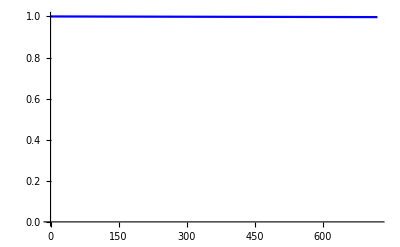

```mathematica
plot1m=ListLinePlot[prob1movr2y, PlotStyle->Blue, PlotRange->{0,1}]
```

```mathematica
probnoreinf3mtimecourse=Take[sarscov2probnoreinfectiontimecourse,90];
probnoreinf3m=Part[sarscov2probnoreinfectiontimecourse, 90];
prob3movr6y=Catenate[NestList[#*probnoreinf3m&,probnoreinf3mtimecourse,23]];
prob3movr2y=Catenate[NestList[#*probnoreinf3m&,probnoreinf3mtimecourse,7]];
```

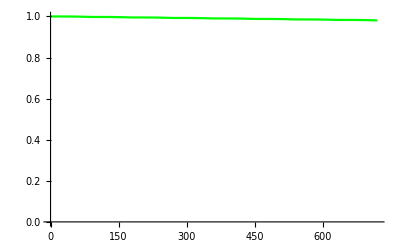

```mathematica
plot3m=ListLinePlot[prob3movr2y, PlotStyle->Green, PlotRange->{0,1}]
```

```mathematica
probnoreinf6mtimecourse=Take[sarscov2probnoreinfectiontimecourse,183];
probnoreinf6m=Part[sarscov2probnoreinfectiontimecourse, 183];
prob6movr6y=Catenate[NestList[#*probnoreinf6m&,probnoreinf6mtimecourse,11]];
prob6movr2y=Catenate[NestList[#*probnoreinf6m&,probnoreinf6mtimecourse,3]];
```

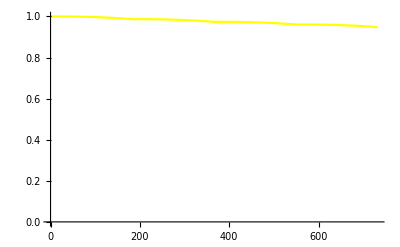

```mathematica
plot6m=ListLinePlot[prob6movr2y, PlotStyle->Yellow, PlotRange->{0,1}]
```

```mathematica
probnoreinf1ytimecourse=Take[sarscov2probnoreinfectiontimecourse,365];
probnoreinf1y=Part[sarscov2probnoreinfectiontimecourse, 365];
prob1yovr6y=Catenate[NestList[#*probnoreinf1y&,probnoreinf1ytimecourse,5]];
prob1yovr2y=Catenate[NestList[#*probnoreinf1y&,probnoreinf1ytimecourse,1]];
```

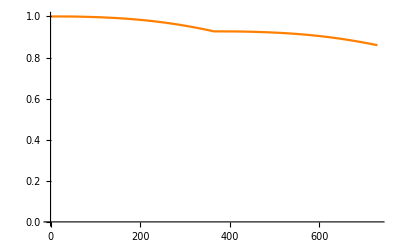

```mathematica
plot1y=ListLinePlot[prob1yovr2y, PlotStyle->Orange, PlotRange->{0,1}]
```

```mathematica
probnoreinf2ytimecourse=Take[sarscov2probnoreinfectiontimecourse,730];
probnoreinf2y=Part[sarscov2probnoreinfectiontimecourse, 730];
prob2yovr6y=Catenate[NestList[#*probnoreinf2y&,probnoreinf2ytimecourse,2]];
prob2yovr2y=Take[sarscov2probnoreinfectiontimecourse,730];
```

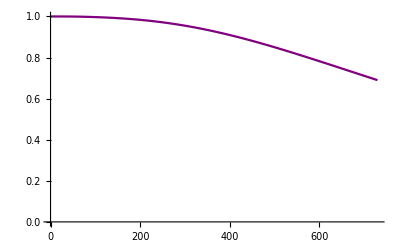

```mathematica
plot2y=ListLinePlot[prob2yovr2y, PlotStyle->Purple, PlotRange->{0,1}]
```

```mathematica
probnoreinf6ytimecourse=Take[sarscov2probnoreinfectiontimecourse,2190];
```

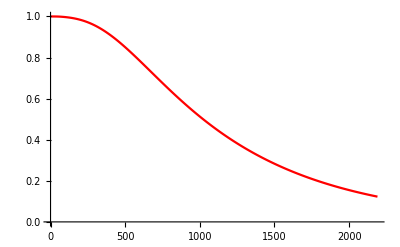

```mathematica
plot6y=ListLinePlot[probnoreinf6ytimecourse, PlotStyle->Red, PlotRange->{0,1}]
```

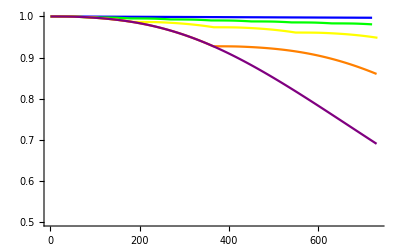

```mathematica
Show[plot1m,plot3m,plot6m,plot1y,plot2y,
PlotRange->{0.5,1}]
```

```mathematica
Export[
StringJoin["/Users/hayley/Documents/townsend/spring-23/cancer/figs/chemo_immuno_boosterovrtime-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
Show[plot1m,plot3m,plot6m,plot1y,plot2y,
PlotRange->{0.5,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability of no reinfection"}]
]
```

/Users/hayley/Documents/townsend/spring-23/cancer/figs/chemo_immuno_boosterovrtime-by-Day_04May2023.pdf

```mathematica
Show[1-Last[prob2yovr2y], 1-Last[prob1yovr2y], 1-Last[prob6movr2y], 1-Last[prob3movr2y],1-Last[prob1movr2y]]
```

Show::gcomb: Could not combine the graphics objects in Show[0.309969,0.139922,0.0518858,0.0192331,0.00316395].

Show[0.309969,0.139922,0.0518858,0.0192331,0.00316395]

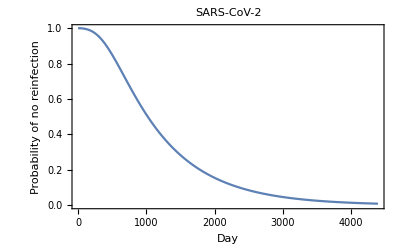

```mathematica
ListLinePlot[sarscov2probnoreinfectiontimecourse,
PlotRange->{0,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability of no reinfection"}]
```

```mathematica
Export[
StringJoin["/Users//jt436/Downloads/Pfizer_alshukairi-gudbjartsson-VoV2_PnorInfTimecourse-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2probnoreinfectiontimecourse,
PlotRange->{0,1},
PlotLabel->"SARS-CoV-2",
Frame->{{True, False}, {True, False}},FrameLabel->{"Day", "Probability of no reinfection"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users//jt436/Downloads/Pfizer_alshukairi-gudbjartsson-VoV2_PnorInfTimecourse-by-Day_04May2023.pdf.

$Failed

```mathematica
sarscov2continuousprobnoreinfection=Interpolation[sarscov2probnoreinfectiontimecourse]
```

InterpolatingFunction[…]

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.95],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{313.331,10.4444,0.858441}

These are the 5% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.50],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{1021.84,34.0615,2.79957}

These are the 50% quantiles (medians) for the probability of no reinfection, in days, months, and years.

```mathematica
{x, x/30, x/365}/.
FindMinimum[{Abs[sarscov2continuousprobnoreinfection[x]-0.05],
1≤x≤4.39*10^3},
 {x, 1000}] [[2]]
```

{2932.92,97.7639,8.03539}

These are the 95% quantiles for the probability of no reinfection, in days, months, and years.

```mathematica
sarscov2probreinfectiondensity={};
day=0;
While[day<4393,
Increment[day];
AppendTo[sarscov2probreinfectiondensity, 
If[day<1201,
sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[day]]]*sarscov2probnoreinfectiontimecourse[[day]],
sarscov2probinfgivenaod[sarscov2antibodytimecourseB[[1201]]]*sarscov2probnoreinfectiontimecourse[[day]]
]
]
];
```

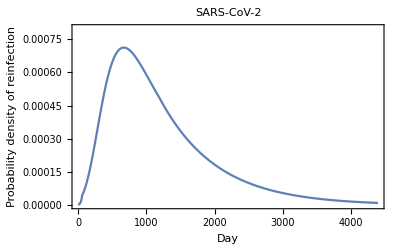

```mathematica
ListLinePlot[sarscov2probreinfectiondensity,
 PlotLabel->"SARS-CoV-2",
PlotRange->{0, 0.0008},
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability density of reinfection"}]
```

This panel is part of Figure 1.

```mathematica
Export[
StringJoin["/Users/jt436/Downloads/Pfizer_alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-Day_", DateString[{"Day", "MonthNameShort", "Year"}] ,".pdf"],
ListLinePlot[sarscov2probreinfectiondensity,
 PlotLabel->"SARS-CoV-2",
PlotRange->{0, 0.0005},
Frame->{{True, False}, {True, False}},
FrameLabel->{"Day", "Probability density of reinfection"}]
]
```

Export::nodir: Directory /Users/jt436/Downloads/ does not exist.

Export::noopen: Cannot open /Users/jt436/Downloads/Pfizer_alshukairi-gudbjartsson-SARS-CoV-2_PrInf-by-Day_04May2023.pdf.

$Failed